# 2021-09-02 · AME beautifier

## https://arxiv.org/abs/2104.05122 Script to generate pictures used in PhD thesis of WB. Please avoid direct copying of these pictures without permission, as it will explicitly clash with already published work; name[at]uj.edu.pl name = w.bruzda

```mathematica
S=ArrayFlatten[Transpose[ArrayReshape[IdentityMatrix[36],{6,6,6,6}],{3,1,2,4}]];

T2[a_]:=Module[{dim,sdim,ret}, (* partial transpose X^Subscript[T, 2] - courtesy of GRM *)
dim=Dimensions[a]⟦1⟧;
sdim=Sqrt[dim];
ret=Partition[a,{sdim,sdim}];
ret=Map[Transpose,ret,{2}];
ret=ArrayFlatten[ret];
Return[ret];
];

(* R2[M_]:=ArrayFlatten@Array[M⟦#2+d#1-d,#4+d#3-d⟧&,{d,d,d,d}] *)
RF[M_]:=Module[{d,ret},
d=Sqrt@Dimensions[M]⟦1⟧;
ret=ArrayFlatten@Array[M⟦#2+d#1-d,#4+d#3-d⟧&,{d,d,d,d}];
Return[ret]
];

Xi[M_]:=1/3(M+RF[T2[M]]+T2[RF[M]]);

SL[M_]:=Module[{d,ret},
d=Sqrt@Dimensions[M]⟦1⟧;
ret=d^2/(d^2-1)(1-Total[Eigenvalues[M.M†]^2]/Tr[M.M†]^2);
Return[ret];
]

ep[M_]:=(SL[RF[M]]+SL[RF[M.S]]-1)//N
gt[M_]:=(SL[RF[M]]-SL[RF[M.S]]+1)//N
```

## numerical AME

```mathematica
numericalAMEfromOCTAVE:={{-0.2502078169183748+0.14874628715859847 ⅈ,-0.11254052073122418+0.06579427776076524 ⅈ,2.6789262753262877*^-7-6.512284361839815*^-7 ⅈ,-5.207250121756767*^-7+8.9081752703557*^-7 ⅈ,-3.674760483524629*^-7+1.5263397655507216*^-6 ⅈ,1.1088593209959696*^-6-1.0323510874626907*^-6 ⅈ,0.030333961347856694-0.2792975621782938 ⅈ,0.39402114978801084-0.04602556390939569 ⅈ,6.85032520986173*^-7+6.469145023575013*^-8 ⅈ,-1.7344739622598274*^-6+1.6624384597402342*^-7 ⅈ,7.899831712676608*^-7+1.1586550930503536*^-7 ⅈ,1.663092684192624*^-7-5.122723598094403*^-7 ⅈ,1.1067617278967545*^-6+1.6135931928847047*^-6 ⅈ,-5.349293202699945*^-7-9.163449588185656*^-7 ⅈ,-0.09947928644777757+0.21530238710239794 ⅈ,-0.3714135412407733+0.13937432955188483 ⅈ,-1.486348257945247*^-7+3.475003622910311*^-7 ⅈ,-1.4596172929065565*^-6-1.546132125372114*^-6 ⅈ,-1.0479564313825573*^-6-4.729458486376985*^-7 ⅈ,8.786721434617117*^-7-9.014525643238901*^-7 ⅈ,-0.46642188932388856+0.1911459756562498 ⅈ,-0.056936535995135755+0.04652786359109379 ⅈ,-1.3917892615136762*^-7+1.0035403473565574*^-6 ⅈ,2.1424052971952268*^-7-7.575345358015739*^-7 ⅈ,5.6098472242527286*^-8+5.171419349969675*^-7 ⅈ,-4.369001724985333*^-7-6.186573231758974*^-7 ⅈ,-3.142544327192076*^-9+3.296398954789198*^-7 ⅈ,2.617517677503626*^-7+6.494149251724812*^-7 ⅈ,0.2987725352882419+0.08054046537597331 ⅈ,0.12165550570386632-0.1684270407317618 ⅈ,-7.243218144159513*^-7+1.9402532062777478*^-7 ⅈ,-8.800848392762073*^-7-7.267982855274635*^-7 ⅈ,-1.123670505698282*^-6-3.705209846854851*^-7 ⅈ,-6.256085134659362*^-7-7.938876269153461*^-7 ⅈ,0.12008281920280446+0.016421280667392193 ⅈ,-0.17651585247162008+0.06398345683725672 ⅈ},{0.3262248209451502-0.0078496798243324 ⅈ,0.03146901724147104-0.19627468073124202 ⅈ,-4.896433271339706*^-7+2.6974578532651394*^-7 ⅈ,7.358156277497731*^-7+8.300121367640911*^-7 ⅈ,5.971894340983663*^-7+4.827027345463349*^-7 ⅈ,-5.983833864346699*^-7+2.2945847230181754*^-7 ⅈ,-0.022143599376248938-0.25129758185793044 ⅈ,0.4393107524053232+0.07295689843672598 ⅈ,1.2858123287565193*^-6+6.919559960710808*^-7 ⅈ,-1.5187484478373925*^-6+9.072518754316139*^-8 ⅈ,8.280373724450091*^-8+6.467312814624481*^-7 ⅈ,4.985733123366587*^-7+3.2955011672330947*^-7 ⅈ,1.7812684180700672*^-7+1.5719525322532846*^-6 ⅈ,1.2028540069541904*^-7-1.2914154925210836*^-6 ⅈ,0.057563481220098314+0.02832817297134803 ⅈ,-0.2048231057223333-0.36061610105910824 ⅈ,6.259142227571513*^-7-7.539317962920733*^-7 ⅈ,-1.6195387822492968*^-8+8.638151359138811*^-8 ⅈ,1.8001500178728425*^-6+9.039270517929854*^-7 ⅈ,-1.1048506567273852*^-6+1.1163766975371031*^-7 ⅈ,0.28464363977847634+0.1017289357601591 ⅈ,-0.026858821669156447-0.1766257133633895 ⅈ,2.6018925797233194*^-7+4.797554220004052*^-7 ⅈ,3.861334877328093*^-7-3.039740562975346*^-7 ⅈ,3.028997157955571*^-8-4.0349182184318266*^-7 ⅈ,-7.178700293514195*^-7+1.1319321654990055*^-7 ⅈ,1.0263682366506988*^-7+4.732520376485305*^-7 ⅈ,5.672686574954844*^-7-4.3859006833985026*^-7 ⅈ,-0.24063335230711577-0.008718953731918229 ⅈ,0.049331146891397656-0.18697515539486492 ⅈ,4.911984537170344*^-8+3.898565434645729*^-7 ⅈ,7.063017254324566*^-7-8.329188951848587*^-7 ⅈ,-7.391678676291202*^-7+3.221053369376059*^-7 ⅈ,2.7188859550580924*^-7-8.297231199674847*^-7 ⅈ,-0.2508513355603647-0.2760711338428232 ⅈ,-0.04789913418130159+0.23629052897291045 ⅈ},{0.21898569226857864+0.4594656271133989 ⅈ,0.10960687706469148+0.11462339782394869 ⅈ,3.474912343842673*^-7-1.2290992112973242*^-8 ⅈ,1.127835568617841*^-7+8.525246692134281*^-7 ⅈ,-2.411147149300463*^-7+1.484239647121105*^-6 ⅈ,-3.1877590282725077*^-7+1.8450230158603698*^-7 ⅈ,0.11499116414440119-0.06815658653228437 ⅈ,0.030171037116046965+0.16678326191441198 ⅈ,2.6607303769618507*^-7+1.5327913376050883*^-6 ⅈ,-5.119557343422759*^-7-2.4725855059942736*^-7 ⅈ,1.2322329626807127*^-7+3.6007155980108396*^-7 ⅈ,7.709244847567409*^-7+4.961283316326504*^-7 ⅈ,3.8135107391769427*^-7+1.9607917218361637*^-7 ⅈ,-2.020797266254898*^-6-2.30670664562449*^-7 ⅈ,0.27616772498896663-0.06218395101874099 ⅈ,-0.049088553239756305+0.28289261538760013 ⅈ,-7.146774634037012*^-7-2.0181589182460824*^-7 ⅈ,-5.68177844467721*^-7+9.506955580690368*^-7 ⅈ,-3.624001680881811*^-7+5.636356291364303*^-7 ⅈ,9.935200528249366*^-8+4.0534462991161086*^-7 ⅈ,0.23453436378751388-0.1706364771949474 ⅈ,0.06691970332857111-0.26034625161739305 ⅈ,2.577026587541331*^-7+2.405251764356353*^-7 ⅈ,1.0040949426429191*^-7+1.1672511882566614*^-6 ⅈ,-1.6266279490376179*^-6-1.0499931931522155*^-6 ⅈ,-4.758521664786561*^-7-1.0143981245686051*^-6 ⅈ,-2.965176160024674*^-7+2.8014581212112977*^-7 ⅈ,8.484036496253511*^-7+1.3970973462076874*^-6 ⅈ,0.18871296919788727+0.5020534547009758 ⅈ,0.1543593386984673-0.036399406859914295 ⅈ,-4.88831144077051*^-7+8.656697619291442*^-7 ⅈ,5.980644045139316*^-7+1.0636652506348931*^-6 ⅈ,3.2904524755253406*^-7-2.141930919778538*^-7 ⅈ,-4.6435403832680017*^-7-5.964383553210689*^-7 ⅈ,0.04624616538229504+0.13689879036174055 ⅈ,0.11331279783743253-0.06076557791657898 ⅈ},{0.21412469336433101+0.13053449018713822 ⅈ,-0.08418995249814741-0.5427184565704037 ⅈ,-6.31107714789414*^-7-1.940385467191774*^-6 ⅈ,1.6785114854353522*^-6+1.064693549952117*^-6 ⅈ,4.980934789344804*^-7+1.144831806944302*^-6 ⅈ,-1.6129762931971214*^-6+1.4803177694339142*^-6 ⅈ,0.035673018132388226+0.17515264013535992 ⅈ,-0.1981374529337252+0.11638622859187556 ⅈ,-1.4861134497775458*^-6+4.6363746175615006*^-11 ⅈ,-6.075804223140691*^-7-4.147667166352897*^-7 ⅈ,-4.534205078465109*^-7-5.650852946820217*^-7 ⅈ,1.1061980822665851*^-7+3.9834009979422547*^-8 ⅈ,6.653693729596899*^-7+1.1973564134348802*^-6 ⅈ,-2.2308601893188465*^-6-2.653577810401986*^-7 ⅈ,0.36458126951070136+0.04710362558964071 ⅈ,-0.3191751033499716-0.024044773069575615 ⅈ,4.7554059114107705*^-7+1.5481521507682006*^-6 ⅈ,-1.5961692051563725*^-6-2.6359597470049234*^-8 ⅈ,-3.9592240262675826*^-7-1.8217668719400226*^-7 ⅈ,-3.6563595223054746*^-7+4.695577196511813*^-8 ⅈ,-0.21627064773510862+0.0014930215007588898 ⅈ,-0.11379068280372431+0.13918384599073091 ⅈ,-8.957060272651862*^-7-2.8753438559292466*^-7 ⅈ,-7.343851670948975*^-7-4.287638343675182*^-7 ⅈ,-1.11696420912466*^-6+1.4720749187333015*^-7 ⅈ,1.0061376553216136*^-6+1.0316710797320106*^-6 ⅈ,-1.1941757809968978*^-6+7.029987608292432*^-7 ⅈ,-2.0140783890676417*^-7-1.7674553965396633*^-6 ⅈ,0.08602053446234086-0.02640574183559871 ⅈ,-0.20121888229848475+0.29975827445133857 ⅈ,8.000683551431798*^-9+4.6425018911111504*^-7 ⅈ,8.414323095229381*^-7-2.974456111831669*^-7 ⅈ,7.165067780453074*^-8+1.0072948307647545*^-6 ⅈ,2.4344991642055724*^-7-3.7732957939434764*^-7 ⅈ,0.18470782324438573-0.04213421250999247 ⅈ,-0.015738224573201842+0.24384261010202218 ⅈ},{0.09263944692471932+0.09445214024728955 ⅈ,0.07507588281086226+0.012103075235580699 ⅈ,-2.4115418449655035*^-7-5.020920208209656*^-7 ⅈ,-2.8136758874197643*^-7+9.941569922497508*^-8 ⅈ,-6.533902867020269*^-8+1.204972019449614*^-6 ⅈ,8.666895854360367*^-7-3.446127601544613*^-7 ⅈ,-0.2222808771437794+0.4240007445178046 ⅈ,0.18971961674344706+0.10872316187355882 ⅈ,-1.038164182190493*^-7-1.279599957715316*^-6 ⅈ,-2.479330943870074*^-7+1.7458835496961256*^-6 ⅈ,-6.432366565500836*^-7+7.110393633845412*^-7 ⅈ,-1.0518265831788165*^-6-2.571229585583007*^-7 ⅈ,-5.980916325670771*^-7-9.688580338007569*^-7 ⅈ,1.8208308871260626*^-7+8.287730410908023*^-7 ⅈ,-0.32863571681901016-0.16345955901725184 ⅈ,0.05792735073137682-0.04604698576720585 ⅈ,-8.114376718465488*^-8-6.634408196148911*^-7 ⅈ,4.457918920831166*^-7-6.966976054678664*^-7 ⅈ,4.7040514929500004*^-8-8.121788629411597*^-7 ⅈ,-1.2234583738682248*^-6+3.206886305257006*^-7 ⅈ,0.02071047767025094+0.24888328474945226 ⅈ,-0.027633494220746926+0.3928745559637929 ⅈ,-5.941441391195054*^-7-2.2338475742268713*^-7 ⅈ,-1.814381865763992*^-6-5.56032529741568*^-9 ⅈ,-5.755737266591177*^-7-6.403975182922572*^-7 ⅈ,-9.534962457855011*^-7+5.514674221007015*^-7 ⅈ,-8.642491979293787*^-7-1.545537679364939*^-6 ⅈ,-3.0491889137229666*^-7+8.79438520166864*^-8 ⅈ,0.11808236920058313+0.4824491499263262 ⅈ,-0.18195342414652965+0.016078972921487474 ⅈ,1.7530522171058105*^-7+1.2602432810857045*^-6 ⅈ,-2.1534987166193975*^-7+2.42126250660224*^-7 ⅈ,2.974198900079772*^-7-6.670475118999986*^-7 ⅈ,4.276266552805108*^-7+1.2474559577535516*^-6 ⅈ,-0.07971629733483995-0.22831453780871228 ⅈ,-0.05653433262876977-0.016953259954025097 ⅈ},{-0.05436325214688495-0.019068688055308744 ⅈ,0.24293618850505935+0.13386344650891624 ⅈ,6.553595521541222*^-7+1.2216991456259763*^-6 ⅈ,-9.971364535801828*^-7+1.252119679814867*^-7 ⅈ,-9.074130752351195*^-9+3.334004261860632*^-8 ⅈ,-1.8738033390891529*^-6+3.02899977638188*^-7 ⅈ,-0.04489938128455519-0.2059691454208502 ⅈ,0.17391943657068787+0.136773167123897 ⅈ,1.2917362801831422*^-6+1.2138029768446468*^-6 ⅈ,-1.829877728305035*^-6+2.9061362103247057*^-7 ⅈ,1.3252967610462296*^-6-9.622742708631504*^-7 ⅈ,-4.395438035105503*^-7-1.4456933606875333*^-6 ⅈ,-1.0585695111101079*^-7+1.020661413678181*^-6 ⅈ,-1.1641422076325014*^-8-1.0407468189754798*^-6 ⅈ,0.12719009255538857+0.11402652920005613 ⅈ,0.010810667734571247-0.20151398218912245 ⅈ,-1.9492287641614814*^-8+9.412041814121919*^-7 ⅈ,-3.7193893374920517*^-7+2.9832128897733234*^-7 ⅈ,-2.0575048316831546*^-7-5.117946187127576*^-7 ⅈ,1.0203129885422157*^-7+2.5995764046382597*^-6 ⅈ,-0.08817160727945514-0.11814308912041845 ⅈ,0.1841340105342765+0.3295723531991386 ⅈ,-5.180908198010314*^-7-2.6363859312317217*^-7 ⅈ,-1.0446211067410838*^-6+3.8976096569665053*^-7 ⅈ,2.7511030936504255*^-7-3.489077291043974*^-7 ⅈ,-1.381913773121357*^-6+8.636181839799528*^-7 ⅈ,-8.06755970805817*^-7+5.200272892025293*^-7 ⅈ,-4.507993697638879*^-7+2.6077422443648857*^-8 ⅈ,0.07717822881175385-0.05013087036630785 ⅈ,-0.16019065174977534+0.01571942902783094 ⅈ,-3.556597009280598*^-7+1.5556259364835068*^-6 ⅈ,1.4885209401876986*^-6+1.5592675407100076*^-7 ⅈ,1.222181477550377*^-7+1.587822007494133*^-6 ⅈ,-3.749386350906936*^-7+1.963481026975855*^-6 ⅈ,0.15167532686910584-0.05691596677215751 ⅈ,0.7290054504730406+0.010889045852526265 ⅈ},{6.10653436088072*^-7+7.52492318184873*^-9 ⅈ,7.696472344755068*^-7-5.28877039288056*^-7 ⅈ,-2.143705911186733*^-7-2.1516228876838558*^-7 ⅈ,5.082275540586877*^-7+1.5029122604620637*^-6 ⅈ,-0.1807361098867598+0.44781535548376267 ⅈ,0.21607425005017064-0.012425342659038316 ⅈ,-3.7750443093731434*^-7+8.89543227220596*^-7 ⅈ,-7.630771138994463*^-7-1.7089855677138166*^-7 ⅈ,1.5588907803509855*^-7-4.870227641590175*^-7 ⅈ,-1.9534766634854428*^-7+1.3217012512917181*^-6 ⅈ,0.051024860417861015+0.12033167985835469 ⅈ,0.07933329226831093-0.2039245122379968 ⅈ,0.06202239766025958+0.399309990273074 ⅈ,0.2669788657407141+0.0983875495862019 ⅈ,3.782272904179207*^-7-7.175218479926748*^-7 ⅈ,2.576406275614507*^-7+2.880894312412563*^-7 ⅈ,-2.8800019390151643*^-8+4.519546339606939*^-8 ⅈ,-1.5891098781861679*^-6-2.470172161747608*^-7 ⅈ,-0.0735222916249621-0.22363287373857257 ⅈ,-0.009529119268095656-0.31527489721765 ⅈ,1.1202950318534022*^-6-6.509339448151907*^-7 ⅈ,5.185689618061873*^-7+7.560433834402636*^-7 ⅈ,6.346714446908708*^-7+8.124868360256942*^-7 ⅈ,2.591703465726347*^-7+8.54637803548476*^-7 ⅈ,4.1905301291500496*^-8+6.023551729784221*^-7 ⅈ,-6.408338037409976*^-7-3.072630601515247*^-7 ⅈ,-0.017257181828386113+0.324292458266876 ⅈ,0.021534581474631994+0.25371550857665487 ⅈ,-9.251928512234163*^-7-1.4698942668381343*^-6 ⅈ,-1.1474314423887133*^-6+3.020108340964084*^-7 ⅈ,6.918976513670128*^-7+4.263683330146817*^-7 ⅈ,-1.4197731232519495*^-6+2.627099420131687*^-7 ⅈ,0.052987169180264186-0.11392096207544633 ⅈ,-0.26376836557425215+0.013181796641324926 ⅈ,-9.33756875431957*^-7+3.1102081914785584*^-7 ⅈ,5.80537621551469*^-7-2.81274911688445*^-7 ⅈ},{-1.0491014593716488*^-6-3.4854663175099004*^-7 ⅈ,-2.0278435890544455*^-7+6.1207777898864*^-7 ⅈ,2.791794411829973*^-7-7.08882037139813*^-7 ⅈ,-2.878160570013444*^-7-1.1438691535636814*^-7 ⅈ,-0.09066648690552265+0.15613709024335334 ⅈ,-0.19910123489898848+0.06536965549255086 ⅈ,-8.246592197100333*^-7+1.8234530973423868*^-6 ⅈ,-5.847230364411371*^-7-8.641771469253268*^-8 ⅈ,-1.9327651311906724*^-6+1.0722191469969555*^-6 ⅈ,-7.984419969214729*^-7-6.148971114505741*^-7 ⅈ,0.08634498427508089+0.22633496172936401 ⅈ,0.03165724202796904+0.42992974518270616 ⅈ,0.07558352209478438+0.2006331911734178 ⅈ,0.1848037418572661-0.08502259161959379 ⅈ,2.898267835310664*^-7-1.22035643811743*^-6 ⅈ,1.6537551086187596*^-7+2.184198836461474*^-6 ⅈ,-6.377008443536353*^-7+3.590976909925714*^-8 ⅈ,-6.581264031385592*^-7+9.97719220064558*^-7 ⅈ,0.507177834916279+0.0448433561948206 ⅈ,-0.23183124107845307+0.157098101789789 ⅈ,-2.097992373065183*^-6+2.605635137931106*^-7 ⅈ,8.966255046483074*^-7-1.307451418963712*^-6 ⅈ,-8.050780602592011*^-8+1.1855455765569234*^-6 ⅈ,-4.413824800861277*^-7-3.6324425982392494*^-7 ⅈ,-1.858719718833557*^-6+3.821465963532722*^-7 ⅈ,1.124261578069885*^-7-1.9832515692902453*^-7 ⅈ,-0.1719267277457165+0.15222156574705303 ⅈ,0.02491125716940565-0.15879613103288148 ⅈ,3.812144085124647*^-8-3.774525150559982*^-7 ⅈ,3.7948805156617915*^-7-1.0445796491467818*^-6 ⅈ,-6.953925106023551*^-7-7.440872051116265*^-7 ⅈ,8.493434411824263*^-7+1.4485792792368057*^-6 ⅈ,-0.3665005245620843-0.10237687534234799 ⅈ,0.10156901060088395+0.142341226476138 ⅈ,3.1800801974374293*^-7-2.0202990429207812*^-7 ⅈ,7.904809399671836*^-7-9.053411945372964*^-7 ⅈ},{-4.2050349019495675*^-7-4.5074369625641724*^-7 ⅈ,-2.7908438099411015*^-7-9.200057252412019*^-7 ⅈ,1.0604689042875703*^-6-8.218015202718366*^-8 ⅈ,7.877956816060294*^-8+2.438573341950745*^-6 ⅈ,0.23654765536632053+0.006274129311352891 ⅈ,0.11056672526161548-0.046727039596128506 ⅈ,-6.494726549483021*^-7-2.6714216464288065*^-7 ⅈ,4.3035684350878345*^-7-1.9436295398134185*^-7 ⅈ,-1.0030898700567805*^-6+1.122291696506461*^-6 ⅈ,-7.038268291029159*^-7+8.969216705109749*^-7 ⅈ,-0.07729017945377231-0.09164775251332102 ⅈ,0.189838287884038+0.36339839264100715 ⅈ,-0.3053799668358114+0.23261162129810065 ⅈ,0.021612028689892565-0.36638155419328655 ⅈ,-4.8838428010067325*^-8-2.028638698227392*^-6 ⅈ,7.111252408181779*^-7+1.6462078629500554*^-6 ⅈ,-8.033831493114985*^-7+1.0052224319601066*^-7 ⅈ,-9.923737116050713*^-7-8.377694773326061*^-7 ⅈ,-0.19301075655110783-0.11325238835283974 ⅈ,0.07553409538467595+0.11922896834260206 ⅈ,4.493633665586527*^-7+7.491929212566362*^-7 ⅈ,-1.552095148509014*^-6+1.2970614145652037*^-6 ⅈ,4.576328324554235*^-7-7.510812251865229*^-7 ⅈ,-8.020416027154642*^-8-4.0024290268343693*^-7 ⅈ,-7.55007571670574*^-7-2.2488578622220645*^-6 ⅈ,5.013576352547178*^-7+1.5477514393770486*^-6 ⅈ,-0.13990609654612676-0.15125981145890222 ⅈ,0.37304090456830563+0.27245618894458395 ⅈ,-8.802142821076608*^-7-1.171184250824131*^-6 ⅈ,-7.798199812836248*^-7+6.444587706683214*^-7 ⅈ,-2.412641155469242*^-7-7.481271924944521*^-7 ⅈ,2.505866412101654*^-6+1.3588632497164158*^-6 ⅈ,0.01022800916739256-0.24787692530277416 ⅈ,0.041912874574854146-0.2755179678301346 ⅈ,5.45294460002621*^-7-1.0515935731925108*^-7 ⅈ,1.670696058442278*^-6-1.2235868492721513*^-7 ⅈ},{-1.5363144186958393*^-6-6.715098368609286*^-7 ⅈ,-1.8972304438331228*^-7+1.205119079337319*^-6 ⅈ,-2.437655490865678*^-6+8.342652981756931*^-7 ⅈ,-4.526547778271883*^-8+5.044735282982993*^-8 ⅈ,0.12285476392592304+0.28342267645768393 ⅈ,-0.08745598701321874+0.21206530047236105 ⅈ,-1.1859922637372233*^-7-1.631782083379163*^-7 ⅈ,-2.741086636004475*^-7-3.2649313011501313*^-7 ⅈ,-9.782923512668962*^-7+2.3844816132018165*^-8 ⅈ,8.795180832070482*^-8+2.537633876295575*^-7 ⅈ,-0.051851103557514294-0.24389589500297176 ⅈ,-0.02373923319564663-0.04971669941181851 ⅈ,-0.13347101627844687+0.19684092877509096 ⅈ,-0.25494578696225084+0.20131272225642816 ⅈ,-1.7961108388295233*^-6+1.3256856401782505*^-7 ⅈ,8.426312474094089*^-7+4.5757690950859464*^-7 ⅈ,-1.3765515850111543*^-7+2.766595235959013*^-7 ⅈ,2.0787721351570032*^-7+3.5449606083926*^-8 ⅈ,-0.08116665840172398-0.021753358592216287 ⅈ,-0.30748385154809543+0.1957458512633692 ⅈ,-1.090437491288454*^-6+1.648089037881162*^-7 ⅈ,7.602219865843196*^-7-2.029542471623791*^-6 ⅈ,-6.477783469835408*^-7+5.974153494819889*^-7 ⅈ,6.084564981578833*^-7+1.083381188267396*^-7 ⅈ,-1.1614558109510065*^-6+1.3050644377121667*^-6 ⅈ,1.587820188306971*^-6-1.7494919358311545*^-6 ⅈ,-0.2890937960186107+0.18281198014457048 ⅈ,0.18244906105133696-0.22974397182320516 ⅈ,-8.502919374223094*^-7+1.5188719094949565*^-7 ⅈ,1.0295607265620177*^-6-1.8125579329397734*^-6 ⅈ,-2.4277129413718956*^-7-4.80761473933139*^-7 ⅈ,-1.2963176236890916*^-6+7.062484557729398*^-7 ⅈ,0.4415257900796379+0.1036423743864104 ⅈ,0.2172225392118309+0.16971208538548677 ⅈ,-8.412485544076475*^-7+5.196231907854745*^-7 ⅈ,-9.734097234873756*^-7+1.382000764822526*^-6 ⅈ},{-7.073678448543675*^-9+1.0837248437638172*^-6 ⅈ,8.107740077922809*^-7-1.3975609482186346*^-7 ⅈ,9.236467423123784*^-7+1.0825067909230436*^-6 ⅈ,-1.9333020980713544*^-6+6.238502921022958*^-7 ⅈ,-0.05886786257751912-0.1228707568492517 ⅈ,0.6140837853685834+0.05727991771861543 ⅈ,3.459952671591715*^-7-4.5903843139821765*^-7 ⅈ,-7.783694464247315*^-7+1.0349734773270864*^-7 ⅈ,-3.422854685146761*^-7-7.363281234566699*^-8 ⅈ,1.572131137701424*^-6-2.2962170038998142*^-7 ⅈ,0.14385988843585348-0.04207347717249236 ⅈ,-0.10213132216721639+0.1559892093118489 ⅈ,0.057777224298310864+0.15822192961063863 ⅈ,-0.39840694366385326+0.04713542963603302 ⅈ,-5.74198593561448*^-7-7.671878485054559*^-8 ⅈ,-2.5076505282689565*^-7-7.413559623831167*^-7 ⅈ,-3.5781649203531565*^-7-1.8857688739715162*^-7 ⅈ,-2.3660692025084806*^-7+6.137153453905642*^-7 ⅈ,0.09318822445938098-0.14363658983631342 ⅈ,0.028470894224106133+0.01963615595177535 ⅈ,5.168316677987492*^-7-1.531062083538759*^-7 ⅈ,9.193671523860179*^-8-1.6918057984885437*^-6 ⅈ,-5.184024981993995*^-7-5.422045954404929*^-7 ⅈ,-7.58581728880353*^-7+6.169253598670155*^-7 ⅈ,7.577593065799526*^-7+3.4386014216569727*^-7 ⅈ,-1.0048784406802014*^-6+2.8879972033268864*^-7 ⅈ,0.0144517512047955-0.20496527892868827 ⅈ,-0.09730961573587213+0.05270370778758098 ⅈ,4.037119454014526*^-7-1.5185470933418155*^-6 ⅈ,-6.060816256474311*^-7+7.141577120679808*^-7 ⅈ,7.905193457682924*^-7-5.242263510681078*^-7 ⅈ,-1.4202568354884475*^-6+1.7489403101138279*^-6 ⅈ,-0.06973645247376908-0.1932841528250112 ⅈ,0.01124121270436688+0.4766335134324418 ⅈ,-1.2775548455246089*^-7-4.939652424595931*^-7 ⅈ,6.386942755648439*^-7+1.965413463894672*^-6 ⅈ},{-1.8874866111739943*^-7+1.2242588151578644*^-8 ⅈ,-7.70412277487087*^-7-9.534991790710601*^-7 ⅈ,-8.886091123812973*^-7+8.681312218677961*^-7 ⅈ,1.1092142106206015*^-7-5.65508451618596*^-7 ⅈ,0.022110555385080083-0.12264363780620538 ⅈ,-0.0670602337351903-0.07762235506661144 ⅈ,-7.753545570102216*^-7+6.523203736202854*^-7 ⅈ,-3.9780120441104683*^-7+4.353196682294058*^-8 ⅈ,2.0109772333465337*^-8+4.2516209410384254*^-7 ⅈ,7.56308294956598*^-7+5.260225067957314*^-7 ⅈ,0.5922056656600585-0.15231995551869149 ⅈ,-0.09384264263714506-0.053752140561665995 ⅈ,-0.09892871959877982+0.06818333696344939 ⅈ,0.1392283209126807-0.03322443317400159 ⅈ,5.676020395917192*^-7-1.389238491800171*^-6 ⅈ,-3.531857919525979*^-7+6.12596648165431*^-7 ⅈ,-9.658666898643142*^-7+1.6656841419146473*^-6 ⅈ,-1.1555999113177506*^-6-2.4415350270701186*^-7 ⅈ,-0.30204285463758135+0.2272897793516631 ⅈ,0.10720182237639278+0.3355730683809988 ⅈ,9.895656009721587*^-7+1.9163791535603547*^-7 ⅈ,-1.5730350351322864*^-6-3.97315051872682*^-7 ⅈ,-2.2102884346397733*^-7+1.0275774854767716*^-6 ⅈ,4.1917624517273655*^-8-1.0129773306251713*^-6 ⅈ,-9.597725093707377*^-7-7.213061191044257*^-7 ⅈ,3.2596016127928173*^-7-4.525405226732393*^-7 ⅈ,-0.3446449552113975+0.1994830248184177 ⅈ,-0.2586819971828919+0.11075791095185557 ⅈ,-7.418549887380776*^-7+4.188713784922249*^-7 ⅈ,2.0268712479232232*^-7-1.151878443916149*^-6 ⅈ,-4.836022430565468*^-7+7.16587770174977*^-7 ⅈ,1.1189895736396505*^-7+1.0207750228904966*^-6 ⅈ,-0.1011425282829434-0.03590370762523381 ⅈ,-0.16812301572056132+0.0942595479705176 ⅈ,7.854612589161536*^-8-1.0821316095768752*^-6 ⅈ,-2.0489416502561877*^-6-9.054570401234585*^-7 ⅈ},{8.360478998955678*^-7-3.4460408001440653*^-7 ⅈ,-9.190808234089963*^-7+8.177684866078616*^-7 ⅈ,0.12595745597966262-0.25014968049704284 ⅈ,0.35757648564013855+0.15033165509713853 ⅈ,-4.221143053151355*^-9-6.509781437232876*^-7 ⅈ,2.401593010934594*^-7+1.9750725940466396*^-6 ⅈ,1.134320185749299*^-6+1.2940619322221458*^-6 ⅈ,-1.0929853495739161*^-6+6.294380780272335*^-7 ⅈ,0.3259130963968826+0.014822381870301419 ⅈ,-0.27270679842621504+0.007649600525247649 ⅈ,2.8597198516167044*^-7+2.6565913972278164*^-7 ⅈ,-5.119236618734632*^-7+6.036121125672921*^-7 ⅈ,-9.736501375562367*^-7-3.423056525730939*^-9 ⅈ,-5.526230512017949*^-7+2.7699900168737246*^-7 ⅈ,-1.3928112004291116*^-6+7.952909257744056*^-7 ⅈ,-1.0591693919703715*^-6-1.1312371049013862*^-6 ⅈ,0.05157956358559702+0.12056241375104992 ⅈ,-0.06983716649559252+0.29607201090387886 ⅈ,2.7113242352660993*^-7+1.1328541991567631*^-6 ⅈ,6.271163893734055*^-7-3.485977946304786*^-7 ⅈ,7.877361627925406*^-8+2.0466657252304898*^-7 ⅈ,5.454269431243164*^-7+5.399379302307994*^-7 ⅈ,0.08952624999133836-0.2076600755367986 ⅈ,0.19309746694961066-0.12458061435339521 ⅈ,0.32499280709447786+0.016572302480744344 ⅈ,0.0009576541281907798+0.047439120772210644 ⅈ,-1.0086898655655393*^-6+8.67376972107925*^-7 ⅈ,-2.056642384590246*^-7-8.048645458308412*^-7 ⅈ,4.5267242176211253*^-7+6.171500641291572*^-7 ⅈ,1.086749578963972*^-7-7.001427739985328*^-7 ⅈ,0.04596355498490071-0.23433703650760984 ⅈ,-0.19226458818360292+0.41763380265950084 ⅈ,-5.950622879169476*^-8+1.3845077080562596*^-6 ⅈ,-2.68679342402961*^-7-4.5766245690068147*^-7 ⅈ,-1.693430895406689*^-7+3.409190399566997*^-7 ⅈ,5.405251124676602*^-7-1.2212385747598087*^-6 ⅈ},{-1.338555840002531*^-6+3.0885919270057185*^-8 ⅈ,1.4435330078221842*^-6-8.627770622590682*^-8 ⅈ,0.2352963679735927-0.17330846350232487 ⅈ,0.3630963877322379-0.38686074074192356 ⅈ,-1.6088633467831182*^-7+6.100661405217256*^-8 ⅈ,1.0700614352741195*^-6+9.104142404264826*^-7 ⅈ,-3.4602970662434007*^-7+9.640531681287534*^-8 ⅈ,1.4046196569507396*^-6+3.028009889355365*^-8 ⅈ,-0.2246781877738064+0.2600671706192801 ⅈ,0.19193566966652278-0.04546571590443695 ⅈ,-1.104851704110052*^-6+7.22852835088883*^-8 ⅈ,-3.7078180248339976*^-8-7.192074917422575*^-7 ⅈ,-3.926666369280518*^-7-6.98469998797191*^-7 ⅈ,-7.589537605809382*^-7-3.582569182442735*^-7 ⅈ,4.146253499912045*^-7-2.2267685746701904*^-7 ⅈ,-3.8532055333939663*^-7+6.014320709998855*^-7 ⅈ,-0.20750013553837926+0.1634421186836299 ⅈ,0.026792088688367514+0.017555244803459373 ⅈ,-6.359202406359953*^-7-7.448150178106239*^-7 ⅈ,3.6808625477474655*^-8-1.112956660928588*^-6 ⅈ,-3.4223266748290015*^-8-9.785212088525563*^-7 ⅈ,5.602969162313287*^-7+8.584140769041237*^-7 ⅈ,-0.18080043331136986+0.16560382414211303 ⅈ,-0.011892038964979632-0.2172873287815229 ⅈ,-0.3836770206915925+0.05744423911554195 ⅈ,-0.21894892245797767+0.029202993469675382 ⅈ,2.631210716773358*^-7-1.180289233987386*^-7 ⅈ,-4.619658633513157*^-7+1.5534422563925898*^-6 ⅈ,-1.1814077666844058*^-6-1.0456003624280397*^-6 ⅈ,9.520637247462105*^-7-8.433003031438346*^-7 ⅈ,0.05654912747359094+0.0783862773493404 ⅈ,-0.20926775953272286+0.21302373187956536 ⅈ,2.766470305615165*^-7+6.817453987104094*^-7 ⅈ,1.3611182786144038*^-6-1.3701858681755552*^-6 ⅈ,-8.754777810066061*^-7-1.6343675625024934*^-6 ⅈ,-2.254564992858199*^-7-2.8199776479220784*^-7 ⅈ},{-6.248358751237416*^-7-3.5278950705208714*^-8 ⅈ,-1.7579272830556961*^-6+1.3098088662635843*^-6 ⅈ,-0.038222927692088855-0.31932819628390474 ⅈ,-0.17625671698131667+0.09380947243289184 ⅈ,2.2814173786245284*^-7+2.52733837441399*^-7 ⅈ,-2.0083810364779353*^-8+3.2198281944839646*^-7 ⅈ,6.834635767061226*^-7-1.4897145880141127*^-6 ⅈ,-2.090839073737305*^-6+1.433479940915472*^-6 ⅈ,0.12706948878283678-0.0597157711211683 ⅈ,0.0465274552471478+0.29040783356654387 ⅈ,-2.8022976157268675*^-7-2.3023509935007902*^-7 ⅈ,-7.778775636818613*^-7+1.3090004235410957*^-6 ⅈ,-2.4253411773540734*^-7-3.929670917279804*^-7 ⅈ,1.4919281177139254*^-7+2.6663853933128756*^-7 ⅈ,-1.7702382876239042*^-7+1.429104929034919*^-6 ⅈ,-6.796936741701454*^-7+6.900238184552597*^-7 ⅈ,-0.1903445871224115+0.08468342220817157 ⅈ,0.11638045804429323-0.0557427791578165 ⅈ,1.257035922236707*^-7+6.807364929910241*^-7 ⅈ,5.658352956322554*^-7-2.272075475782953*^-7 ⅈ,1.5911329403588137*^-6+1.1736978779083862*^-6 ⅈ,-9.443051332886547*^-7+1.0706906191804836*^-6 ⅈ,-0.1038743835576293-0.15562552121350917 ⅈ,0.6313104156105913+0.052716368350922374 ⅈ,-0.1390820183380504+0.1848449275917603 ⅈ,-0.19391172826843964+0.16637075711185867 ⅈ,-9.583584084822683*^-8+5.742689687254776*^-7 ⅈ,-5.084097555729805*^-7-7.748960804201954*^-7 ⅈ,-8.574209975770186*^-7+3.8155285862762067*^-7 ⅈ,-4.922530019435545*^-7+8.015601102862036*^-7 ⅈ,0.12026852624899849+0.25600726997794404 ⅈ,0.21458174438022534-0.09618032134282578 ⅈ,3.756020501774482*^-7-9.136385126298774*^-7 ⅈ,2.2656780074986616*^-7+1.2241540821994468*^-6 ⅈ,-6.506325580524219*^-7-5.874871907562973*^-7 ⅈ,-5.029791921157267*^-8-1.1297929725269384*^-7 ⅈ},{-1.319251753652273*^-6+6.347184550864472*^-7 ⅈ,-1.6309809990414093*^-7-1.3844974512816632*^-6 ⅈ,-0.10969895613708872+0.22554571277900123 ⅈ,0.10119258433503867+0.1700590419251844 ⅈ,-5.081559587196555*^-7-6.318769561058923*^-7 ⅈ,-4.660616736169159*^-7-3.46557036207118*^-7 ⅈ,-8.897664592594614*^-7+1.133573012054856*^-6 ⅈ,3.1293833153284156*^-7-2.9889020046816595*^-7 ⅈ,0.013931011467064505+0.28364519417082595 ⅈ,0.1720158112862953+0.12899451585604194 ⅈ,1.554149743482336*^-7+5.034756349817093*^-7 ⅈ,-8.64466520034135*^-8+1.1104145733326076*^-6 ⅈ,-2.3579726851630234*^-8+2.859556236245453*^-8 ⅈ,-2.911432824995001*^-7-1.857883148576045*^-7 ⅈ,-1.5885606337306957*^-7+7.954408714054041*^-7 ⅈ,4.751132941941197*^-7-5.514573810788681*^-7 ⅈ,0.5067528055118612-0.3746061436231189 ⅈ,0.06761885521243458-0.03176643083611182 ⅈ,-3.8909708593992676*^-7+4.4013591368741167*^-7 ⅈ,3.08346671987203*^-7-9.946136318023102*^-7 ⅈ,-5.048550497793736*^-7+4.005812591356683*^-8 ⅈ,-1.2932160065662335*^-6-3.75780490058375*^-8 ⅈ,-0.040505739677409676+0.28036485727337973 ⅈ,0.31803561669146124-0.004326255865307264 ⅈ,-0.14827257779866646+0.18405989827436858 ⅈ,-0.044996119632482456-0.025736473475506172 ⅈ,1.612765615083278*^-7-1.4692179164249586*^-6 ⅈ,-6.457499786421961*^-7+4.5401913262299587*^-7 ⅈ,4.755437871661189*^-7+1.901275431103605*^-7 ⅈ,-1.0973538781267056*^-6-2.0676151707421653*^-8 ⅈ,-0.1798702641930331-0.09254079790199528 ⅈ,0.05161139054923333+0.2912160197032181 ⅈ,2.5455489467782894*^-7+1.5445429406638067*^-6 ⅈ,-1.622377612794934*^-6-2.496274185050801*^-7 ⅈ,1.9060237467158347*^-7+6.934234383568216*^-7 ⅈ,1.0680212464003747*^-6-3.3836989865587697*^-7 ⅈ},{-1.3349542469856539*^-6-2.9788514199768917*^-7 ⅈ,2.0029596632317737*^-6+1.8970846349386505*^-7 ⅈ,-0.31448541182385703-0.08081382463168951 ⅈ,0.006736756902368399+0.06181068163711152 ⅈ,-2.7748689904703855*^-7-7.547831614440614*^-7 ⅈ,-2.1308840560899792*^-7-2.0876703268023209*^-7 ⅈ,-7.893147994948029*^-7+4.4622825827456136*^-7 ⅈ,8.362844035950112*^-7-1.2984533138415966*^-6 ⅈ,0.054975240381857735+0.3961192076987583 ⅈ,-0.03379302285965409-0.1359341139447854 ⅈ,-2.375176234303833*^-7-2.4018931399361065*^-8 ⅈ,-1.1319312588041475*^-6-5.069110277852729*^-7 ⅈ,-6.595110720875041*^-7+1.0744937169876456*^-6 ⅈ,7.154152668886749*^-7+9.001693004398459*^-7 ⅈ,-1.4192603350407507*^-6-5.340788435080623*^-7 ⅈ,-7.138280451730698*^-7+3.3810506208653557*^-7 ⅈ,-0.08466811041170216-0.2159603486627599 ⅈ,-0.03700327337314638+0.33996625245145773 ⅈ,1.9734498853812843*^-7-9.073263956063671*^-7 ⅈ,8.273368511807488*^-8+5.183636342526166*^-7 ⅈ,-8.77604791451117*^-7-7.50775938376802*^-7 ⅈ,-4.468725422548947*^-7+9.551306165422879*^-8 ⅈ,-0.2523179290727075-0.04454642156323333 ⅈ,-0.044613908073610195+0.007453014398040433 ⅈ,0.0038953665128199227-0.19912094904184932 ⅈ,0.251512733792184-0.2325868259186355 ⅈ,1.8158316964361765*^-6-6.648097937364539*^-7 ⅈ,-1.5684121362768977*^-9+8.052034631052946*^-7 ⅈ,-4.919636212297185*^-7-9.031978862351907*^-7 ⅈ,-6.025221239505663*^-7+3.174731588451163*^-7 ⅈ,0.40912344775876586+0.3627439548033613 ⅈ,0.11268890044307872+0.06338180119790257 ⅈ,-3.440383350428178*^-7-2.3730035219118872*^-7 ⅈ,-5.996828283082178*^-9-1.1164964367274544*^-7 ⅈ,1.1227439448112386*^-7+8.295490678163208*^-7 ⅈ,-1.2051610769128751*^-6+5.410205762938769*^-7 ⅈ},{2.714198546801411*^-7+7.789691732484895*^-7 ⅈ,-5.20260295719388*^-7+6.59657626148058*^-7 ⅈ,0.15697386283574932-0.1024459810644896 ⅈ,-0.11779645423604673-0.022937528180692307 ⅈ,2.23168252586059*^-7-1.4844652994339125*^-7 ⅈ,-4.827022733328024*^-7+4.506235826984284*^-7 ⅈ,-7.045933822502627*^-9-1.3479515281605847*^-6 ⅈ,2.941104348258561*^-7+1.821291004802661*^-6 ⅈ,0.18343636788028014-0.10372241504989428 ⅈ,0.33940095024595857+0.29977816045677036 ⅈ,-1.179698944621388*^-6+1.4416583347942602*^-7 ⅈ,-5.645247255076091*^-7+1.6569101091296057*^-6 ⅈ,5.924936089390931*^-7-5.027291493306385*^-7 ⅈ,-5.061541733311636*^-7+1.173948388446047*^-6 ⅈ,-8.805585699420138*^-7-3.759508117040511*^-7 ⅈ,-1.2610323374406818*^-7-1.1578513735427398*^-6 ⅈ,-0.19486557367164475+0.006785131489836603 ⅈ,-0.266988812066218+0.27686394493903216 ⅈ,-3.81723418726651*^-7-5.346435001732375*^-7 ⅈ,-2.3233382409615366*^-7+1.7155000078122873*^-7 ⅈ,1.2128618592788243*^-7-7.288294020281472*^-7 ⅈ,-5.26556835848957*^-7+1.4290175481997125*^-6 ⅈ,0.07968408638222009+0.28666043367320315 ⅈ,0.053985473481096585+0.1081772247416333 ⅈ,-0.2136178127083579-0.10023021567839299 ⅈ,0.5469744758210772+0.05772941719825675 ⅈ,2.0383252246607836*^-6+9.541705392121515*^-8 ⅈ,-2.3730810760208554*^-6+1.0350855143767546*^-6 ⅈ,-3.352750918023811*^-7-3.9877160232064385*^-7 ⅈ,-1.1745102583941847*^-6-1.2101466629818591*^-6 ⅈ,-0.04380706256131418-0.22517903145732562 ⅈ,-0.026265138310321554+0.019797967091696747 ⅈ,7.435931713359323*^-7+2.350794122002453*^-7 ⅈ,3.168698717304075*^-8-1.1259439019750683*^-6 ⅈ,7.808386015689672*^-7-2.922695367113537*^-7 ⅈ,3.59286688594862*^-8+7.907915524751202*^-7 ⅈ},{2.67434124284713*^-7+1.5672862141120623*^-7 ⅈ,2.343783226351533*^-7+1.7924402982705256*^-7 ⅈ,-9.67841799343061*^-8+6.609477290475674*^-8 ⅈ,-1.6750620371736025*^-6+1.3689397233146439*^-7 ⅈ,-0.12318680137491132-0.16589617169286913 ⅈ,0.15232163566184068+0.07905138960945371 ⅈ,-8.326367568339821*^-8-2.2424417411110936*^-7 ⅈ,8.341342224715831*^-7-1.620499379684226*^-7 ⅈ,5.210086679611689*^-7-3.0259600315024615*^-7 ⅈ,5.795473614037156*^-7-4.277427006968426*^-7 ⅈ,-0.17187571708647986+0.25863441868390447 ⅈ,0.0326171433795938-0.22127518634609095 ⅈ,-0.21414042136078248+0.3119791597394748 ⅈ,0.29458968146029346-0.3022698944262767 ⅈ,8.279157617578853*^-7-1.8053194595427091*^-6 ⅈ,-1.6187918214227714*^-7+3.2028503020829764*^-6 ⅈ,-4.914192757721203*^-7-2.6511116484051467*^-7 ⅈ,-1.3026009971217611*^-6-1.8705749278702388*^-7 ⅈ,-0.22897933097117346+0.15539843997064956 ⅈ,0.0262473326900124+0.008003967496655745 ⅈ,4.781850588692071*^-7-7.897954742916435*^-7 ⅈ,-2.667663911437579*^-7-6.921897769546215*^-8 ⅈ,-1.556392013601915*^-7-3.079395145613728*^-7 ⅈ,6.014739033222138*^-8+1.586150318380608*^-7 ⅈ,-5.851658575126151*^-7+1.4542163492836657*^-7 ⅈ,2.0557486286876259*^-7-1.154470197356483*^-7 ⅈ,0.04976038814687336-0.025481734927157232 ⅈ,-0.06632908565614087-0.10352495374097448 ⅈ,2.6497030791716725*^-7-1.6234570390794012*^-7 ⅈ,-1.34447374491517*^-6-1.1915689122204975*^-7 ⅈ,-1.1824198973674899*^-6-6.269186825554746*^-7 ⅈ,8.852234105057552*^-7+9.647238744213416*^-7 ⅈ,-0.059596266892171644+0.2931658571233751 ⅈ,0.45336182889801224+0.26352441305120616 ⅈ,6.50486699903946*^-8+1.0468359166321273*^-7 ⅈ,-9.717003022862141*^-7+8.139859513853209*^-7 ⅈ},{-4.2058183727378145*^-7-2.8842066424929213*^-7 ⅈ,2.620262116968808*^-7+5.121397211177436*^-7 ⅈ,5.955874160315511*^-7+2.9521232766845096*^-7 ⅈ,-3.9223238323948806*^-7+9.313742086874965*^-7 ⅈ,-0.1472464479722135-0.024233377571789363 ⅈ,-0.18200024405211762+0.35725180755811314 ⅈ,-5.791114649489337*^-7-4.3913857306759896*^-7 ⅈ,-6.393639974539012*^-7+3.167373082146874*^-7 ⅈ,-9.482589034826017*^-8+4.443982415808234*^-7 ⅈ,-3.1451928410655694*^-7+2.4942686708412376*^-7 ⅈ,0.2975862806893275+0.06546194029283242 ⅈ,0.01655625058693974+0.10877467787044928 ⅈ,-0.06710093976012525+0.2000526883206892 ⅈ,-0.1549866610997106+0.39202677400963726 ⅈ,-5.258503713578833*^-7+4.122983247450973*^-7 ⅈ,-9.069243911419278*^-9-3.8066146018644886*^-7 ⅈ,-6.082324655320992*^-7+1.184535523141017*^-7 ⅈ,5.782695154388229*^-7-7.369870579088111*^-7 ⅈ,-0.2769742867527322+0.1135290704495961 ⅈ,-0.12095488173953493-0.022023325590311595 ⅈ,-9.857669840129812*^-9+1.9091762428445624*^-7 ⅈ,3.6813343512465124*^-8+8.71920017880834*^-7 ⅈ,-4.778921416943166*^-7-1.6088797870350557*^-7 ⅈ,-2.988349707619409*^-7-1.6095017069985007*^-7 ⅈ,6.529941104886638*^-7-7.614887174711704*^-7 ⅈ,-1.6396404801458098*^-6+1.0386648881047233*^-6 ⅈ,0.45302730405735797-0.07538166013702721 ⅈ,0.1701366053666015+0.15269752230882513 ⅈ,2.0644438987471592*^-7+2.5053576682698697*^-7 ⅈ,-9.582747000393133*^-7+3.3690328762187027*^-7 ⅈ,-1.6807891201932323*^-6-1.8345477852121927*^-7 ⅈ,8.378084072648006*^-7-4.6678723398391186*^-7 ⅈ,-0.24930670172492625-0.02840719355389207 ⅈ,0.18287618254366478-0.159679580735226 ⅈ,-1.2948482454450128*^-6-2.401127812481918*^-7 ⅈ,8.821834536834606*^-8+1.7793567262929658*^-7 ⅈ},{-4.549326430014489*^-7+1.6411908268509914*^-7 ⅈ,-5.20509684569237*^-7+7.99995392944397*^-7 ⅈ,-9.808026500204845*^-7-5.870894705661822*^-7 ⅈ,2.43144423766814*^-7+3.7687868788272016*^-7 ⅈ,0.4332497818910701+0.10590269172365344 ⅈ,-0.02101545285491043+0.022052559194965515 ⅈ,-1.5968926726592917*^-6-2.599301180405966*^-7 ⅈ,4.003852980410949*^-8+1.272936543558062*^-6 ⅈ,-1.7991116994624246*^-7-3.818947845526943*^-7 ⅈ,-2.393496753502755*^-7+1.454800049455196*^-7 ⅈ,-0.07053052760701944+0.4251306041018156 ⅈ,-0.11614493974901463+0.1755272918124487 ⅈ,0.05782493204275456+0.06199475081234916 ⅈ,-0.08271432254766825+0.2685246601299051 ⅈ,-5.522536780924388*^-7+1.3672928535074513*^-6 ⅈ,-4.231747051386403*^-7-9.500528461506285*^-7 ⅈ,-5.522256087200916*^-7-5.305018658634252*^-7 ⅈ,2.7860937640289407*^-8-4.678115050234244*^-7 ⅈ,0.05186169778039769+0.16449847485065544 ⅈ,0.36988428490180003+0.04470266883057755 ⅈ,6.076828637791021*^-7-9.685823770810842*^-7 ⅈ,-6.416442849821458*^-7+1.1307062360160769*^-6 ⅈ,-2.700119294679615*^-7+1.8469055806935586*^-7 ⅈ,-1.4445896227427424*^-6-3.627103174752566*^-8 ⅈ,-3.638246769514797*^-7-9.845305390665526*^-7 ⅈ,-7.410394652351826*^-7+1.0703680926975323*^-6 ⅈ,-0.11594791300103094-0.011881073889472543 ⅈ,0.09862089377334858+0.2961849203202207 ⅈ,-1.064465095859668*^-6-4.6840072822490475*^-7 ⅈ,-1.0890348465381061*^-7+5.578447386939134*^-7 ⅈ,-2.772618089494361*^-7+7.968717073147946*^-7 ⅈ,-6.029331613421895*^-7-1.2477953634498077*^-6 ⅈ,0.05206546663741131+0.41573084998530513 ⅈ,-0.09874484853799484+0.13825604524758028 ⅈ,4.494404714575073*^-7+1.2910382926958897*^-6 ⅈ,-1.456306116645427*^-6-6.641461813027048*^-8 ⅈ},{2.09584037402788*^-7+3.2392192524793867*^-7 ⅈ,-6.798910377678324*^-7-2.373743940888018*^-7 ⅈ,6.133287513768182*^-7+2.0923518242663142*^-7 ⅈ,-2.832652573198091*^-7-1.1370616356809471*^-7 ⅈ,-0.06546769105865397+0.133302620006165 ⅈ,-0.00609981024476465-0.251495391648957 ⅈ,-1.608251790291906*^-7+9.034573135030532*^-7 ⅈ,7.31206978940406*^-7-6.720943891078135*^-7 ⅈ,2.9207942205122794*^-7+8.201399303436885*^-7 ⅈ,-7.733197391890378*^-7+1.592745284056604*^-6 ⅈ,0.00935967208011618+0.11484230868267012 ⅈ,0.5969100726699201+0.06544904791531715 ⅈ,-0.11534692956538697-0.04535125580937599 ⅈ,-0.05281324723338418+0.006607063454572626 ⅈ,1.668924264619509*^-7+9.349046276464074*^-7 ⅈ,-4.797149644845955*^-7-8.386030768969821*^-7 ⅈ,-9.629197371407994*^-8+4.1346420422833097*^-7 ⅈ,-3.8290728841122723*^-7+6.380394037552861*^-7 ⅈ,0.07581791737576896+0.3606456753266015 ⅈ,-0.15920229295589527+0.2195988256797025 ⅈ,-1.260848172938457*^-6+4.654000125975388*^-7 ⅈ,-4.956006398326718*^-7-4.5997686323653164*^-7 ⅈ,-7.922381994179828*^-7+3.5325836281185907*^-7 ⅈ,-4.999552909099036*^-7+7.277824865190019*^-7 ⅈ,1.064443987432162*^-6-1.5417560869646074*^-7 ⅈ,-2.0259267041276147*^-6-2.804918687177027*^-7 ⅈ,0.3180503188127352-0.049723939864180736 ⅈ,-0.18007569522452138+0.15119719991262803 ⅈ,2.2301620965226032*^-7-7.382607430106436*^-7 ⅈ,-1.109819922639338*^-6+1.3504530636671008*^-6 ⅈ,1.4748304678069424*^-6+1.7581147911810424*^-7 ⅈ,-2.0475763612276543*^-6+2.9116510133530074*^-7 ⅈ,0.3130003860685122-0.06545231410166805 ⅈ,-0.11959634397728638+0.19428228636923328 ⅈ,-2.385103347601891*^-7+3.9386888417512056*^-7 ⅈ,1.4831141654375601*^-7-1.1218873811537247*^-6 ⅈ},{1.2516915291020671*^-6-7.625327667140637*^-7 ⅈ,-7.176331247964185*^-7-6.698140743374714*^-7 ⅈ,5.149664724004438*^-7-7.511925907907613*^-7 ⅈ,6.438175983794481*^-7-9.941899705989687*^-7 ⅈ,-0.40548163453589564-0.0020521914000894634 ⅈ,-0.27114333412299235-0.11624656451415652 ⅈ,2.719965247685585*^-7-1.3664086371753537*^-7 ⅈ,6.451067470492067*^-8+5.636725061708425*^-7 ⅈ,-7.813679550605634*^-7-9.922719720351775*^-7 ⅈ,6.457963671966521*^-7-4.948063039716954*^-7 ⅈ,-0.037330950231773144+0.04900953927765895 ⅈ,-0.1562719213207001+0.1867102839631306 ⅈ,0.23816069967090903+0.15410286598302936 ⅈ,0.12067754730780873-0.02588771762603896 ⅈ,-3.405285550102388*^-7+1.2505549586610055*^-6 ⅈ,8.101786989067605*^-7+6.26839786410649*^-7 ⅈ,4.889501645163885*^-7+4.2223130307730833*^-7 ⅈ,-4.3208060344218646*^-7-1.0196166412568264*^-7 ⅈ,-0.1785837052731138-0.27727729104153076 ⅈ,0.3178288747353858+0.3492292021698866 ⅈ,1.149293602273338*^-6+1.595571274732449*^-6 ⅈ,-1.820748261448929*^-6-3.5696333272605685*^-7 ⅈ,-9.878960519071889*^-8-6.292864654505737*^-7 ⅈ,-1.4066105127885642*^-8-1.134479635081509*^-6 ⅈ,5.303645400772661*^-7+1.9677284865404765*^-7 ⅈ,-4.282559253054874*^-8+1.5109903056531593*^-6 ⅈ,0.15925214754465356-0.18029366395120505 ⅈ,0.18866339914791064-0.15251381855846385 ⅈ,1.89464927965316*^-7-1.8352654968661897*^-8 ⅈ,1.6086329982581415*^-6+3.0451388952426606*^-7 ⅈ,1.2992451277685224*^-7+4.298867876811885*^-7 ⅈ,-1.391199369732421*^-6+8.230985079071829*^-7 ⅈ,0.2816176422460272-0.0007396540615580843 ⅈ,-0.15761556707096025+0.19273208304573675 ⅈ,1.5385060146005936*^-8-3.0731022411523146*^-7 ⅈ,-5.813393373702014*^-7+8.979947516835063*^-8 ⅈ},{9.54445997337211*^-7+3.768271395199198*^-7 ⅈ,-1.0919980732160273*^-7+9.16025963512701*^-7 ⅈ,-8.30560962145066*^-7+3.647773848362845*^-7 ⅈ,-1.1053445718445243*^-6-3.9278031119423235*^-7 ⅈ,-0.06743151324039608-0.3062345081966673 ⅈ,-0.15061216956081158+0.29525775339039706 ⅈ,4.794794632584365*^-7+2.8288518591143563*^-7 ⅈ,-3.053249209850062*^-7-8.824979261246035*^-7 ⅈ,6.185889256382637*^-8-4.447957437092587*^-8 ⅈ,-9.379103390327881*^-7+7.006100188750031*^-7 ⅈ,-0.24341992984274521-0.0007490438668708611 ⅈ,0.14955617117204548-0.0046694806061025745 ⅈ,0.5023439902669042+0.03044434986370565 ⅈ,0.04786843886607711-0.028901373320430662 ⅈ,-9.818602767219797*^-7+1.4115795385349905*^-7 ⅈ,1.0243737026682798*^-7-1.1385703052313456*^-6 ⅈ,9.382140093230906*^-7+6.102979725492591*^-7 ⅈ,-3.8676770864470855*^-7+3.7473955768162204*^-7 ⅈ,-0.12283786262303285-0.019625426876791044 ⅈ,-0.3032204973103516+0.028901303903246398 ⅈ,-1.505649221224259*^-6-5.605265670435844*^-7 ⅈ,4.028756665011568*^-7-1.1485714874273373*^-6 ⅈ,-1.6625099140410438*^-7-8.186255509440299*^-7 ⅈ,1.7276272331126497*^-7+2.2037286515064203*^-7 ⅈ,7.334768809402759*^-7-7.693817619044974*^-7 ⅈ,-7.577589217697134*^-7+1.1905479355978077*^-6 ⅈ,-0.2897720368351042-0.09205687895811929 ⅈ,-0.12591728193807009+0.4728706384037695 ⅈ,4.7215675305634086*^-7-2.2140844012363825*^-7 ⅈ,-8.155316316843519*^-7-8.33487711366515*^-7 ⅈ,3.800874866649595*^-7+9.9158628326379*^-7 ⅈ,-5.136006907585818*^-7+5.126193979715366*^-7 ⅈ,0.08047519493010674-0.04894189403870851 ⅈ,0.010386153724213462+0.06804967788130736 ⅈ,1.9664877726199848*^-7-5.770566428933699*^-7 ⅈ,-5.752895649024925*^-7+6.310361161110389*^-7 ⅈ},{-1.5151453484858417*^-6-4.1640538705462304*^-7 ⅈ,1.0313324853017392*^-6+5.996944978832464*^-7 ⅈ,-0.371133877324771-0.0713229602449482 ⅈ,0.2390203580351239-0.12487599003131906 ⅈ,-1.3156098823408069*^-6-7.699614179151881*^-7 ⅈ,4.795132183960105*^-7+1.1995156554145403*^-7 ⅈ,-4.695765540296826*^-9-8.898764625037137*^-7 ⅈ,9.362487712362421*^-7+1.7580407068642362*^-6 ⅈ,-0.33930344357855174-0.09592936798721542 ⅈ,0.08187432519092352+0.20366101700360462 ⅈ,-2.2283286684257608*^-7-7.368320450139298*^-8 ⅈ,7.391023770786376*^-8+3.153446305713403*^-7 ⅈ,-5.847692501892432*^-7-1.3803648725094209*^-7 ⅈ,-8.735041076290972*^-7+7.85829298230456*^-7 ⅈ,3.4863355856395994*^-7-4.6162138478411663*^-7 ⅈ,-5.168550383412296*^-7-9.9930868975584*^-7 ⅈ,-0.02451822511169616-0.14111332319295522 ⅈ,-0.2204565096439609+0.08917339445139322 ⅈ,-4.548730405465329*^-7+6.697202054282979*^-7 ⅈ,4.890557110115434*^-7+4.977109973117178*^-7 ⅈ,-8.096967437469516*^-7-7.219762317364764*^-7 ⅈ,3.5203247117365777*^-7-2.6076843462341515*^-7 ⅈ,0.5593437994287225-0.004667246715036488 ⅈ,-0.001971294764721279+0.1868682814804005 ⅈ,0.01151891232171823+0.013378562037479017 ⅈ,-0.21756751470452357+0.05707667638291567 ⅈ,-3.3069963652210266*^-7-5.541918211490748*^-7 ⅈ,-5.222731315479567*^-7-5.389942190556218*^-7 ⅈ,-5.771941869459063*^-7+5.869213412596982*^-7 ⅈ,-9.574984061819919*^-7-5.820270967751839*^-7 ⅈ,0.3449949543314584-0.11078854379301238 ⅈ,0.06659334563274125+0.020594299066302262 ⅈ,-8.768337909268417*^-7+5.087319622093522*^-7 ⅈ,1.1041840143333204*^-6-1.1424056634706803*^-6 ⅈ,1.471302472955821*^-6+5.874088626432045*^-7 ⅈ,-3.803351756662132*^-7-2.1472616464415784*^-7 ⅈ},{-3.6750313346656243*^-7-8.439457840625498*^-7 ⅈ,-4.0746085783888164*^-7+2.162175574638159*^-6 ⅈ,0.03984900383550978-0.012509632945439761 ⅈ,0.1232376379872508+0.3826015709255881 ⅈ,-3.969548581089777*^-7-5.010697478350853*^-7 ⅈ,1.0215247808753602*^-7+1.8038597719705063*^-8 ⅈ,8.699947318668855*^-7-2.829185253522357*^-7 ⅈ,-9.196703347341684*^-7+4.064065557696228*^-7 ⅈ,-0.09595325936706721+0.13907594936112444 ⅈ,-0.1490068281745996+0.11820171667431234 ⅈ,-7.788186854318369*^-7+1.4422041462458512*^-7 ⅈ,-1.2162444514504656*^-6-7.637496108187092*^-7 ⅈ,-8.267881916185216*^-7+1.6543235312888038*^-7 ⅈ,5.001641039271282*^-7+1.7213438249091828*^-7 ⅈ,3.638024401869666*^-7+6.232692549013041*^-7 ⅈ,-9.12445119044536*^-8+3.3399948567991444*^-7 ⅈ,-0.0408898126600255+0.03874160543379024 ⅈ,0.5104907244087651+0.21075677661480996 ⅈ,-7.931756207738005*^-7+4.0592477274815903*^-7 ⅈ,-9.211438207860911*^-7-1.1249783840941441*^-7 ⅈ,-1.319500155978759*^-6-1.569533383122268*^-7 ⅈ,9.111030041773771*^-7-8.82672426087694*^-8 ⅈ,0.2634478808137113+0.02425308538778539 ⅈ,-0.28072844742352293-0.06141110090917004 ⅈ,-0.24265778447644015+0.04059536948892065 ⅈ,0.15178716034994344+0.45063998435861646 ⅈ,4.6970816411189*^-7+5.431951760406784*^-7 ⅈ,-2.1795897197120218*^-6-8.22279229657774*^-7 ⅈ,-4.886166795406433*^-7+7.315152337344921*^-8 ⅈ,1.2951450609026416*^-7-9.10569899974234*^-7 ⅈ,-0.03918831992041328+0.13268229055106662 ⅈ,0.032336123967701996-0.06605246916958678 ⅈ,1.0559201125970308*^-6-9.174032546410693*^-7 ⅈ,-5.353633046878414*^-7+1.6868605422493133*^-6 ⅈ,-6.429954399200799*^-7-1.7329285720291132*^-7 ⅈ,-1.357162246876098*^-6+7.705549094905173*^-7 ⅈ},{4.3590346039332217*^-7-1.2162612339425285*^-6 ⅈ,-2.2881919882131174*^-6+3.0801354553022797*^-6 ⅈ,0.10538296722729763-0.2531644840906864 ⅈ,0.164800364040375+0.3681778259410871 ⅈ,-3.164790531480499*^-7+1.4346134961928936*^-7 ⅈ,-3.0550870021295307*^-7+1.2510800187423565*^-6 ⅈ,-1.8538167305959252*^-6+3.639579564743145*^-7 ⅈ,8.48273333520222*^-9-6.128556730988777*^-7 ⅈ,0.09766310574484743+0.22250575561912692 ⅈ,0.22034256175045364-0.10836153583044604 ⅈ,2.628472110591251*^-7+6.702341441566784*^-8 ⅈ,-1.2492975450511393*^-6-4.759118590463851*^-7 ⅈ,4.457147561309771*^-7-1.5907606671188013*^-6 ⅈ,5.574061268734387*^-7+9.43293304168924*^-7 ⅈ,-1.40574822858619*^-7+4.4100834840909986*^-7 ⅈ,5.481426491940611*^-7-2.5015471504657993*^-7 ⅈ,0.08283845505731356+0.12156550667789282 ⅈ,-0.2792314481686509-0.14131099260099164 ⅈ,6.030823072669667*^-7-5.32538809806804*^-7 ⅈ,-1.3534634622121289*^-6+5.159213249672501*^-8 ⅈ,-3.362264582073074*^-7-4.301007444119931*^-7 ⅈ,5.672132961792586*^-7+1.214809422500629*^-7 ⅈ,-0.0698558249518639-0.1842685777102091 ⅈ,-0.23361475083494648+0.03345775397927485 ⅈ,-0.19824281874622576-0.12355368406072231 ⅈ,-0.19207151463937278-0.0348268371864877 ⅈ,3.7755517101611957*^-7+1.7328118336046305*^-7 ⅈ,-1.8775604626562747*^-6-3.442687625671015*^-7 ⅈ,-5.350847581270246*^-7-1.3729378519483637*^-7 ⅈ,5.126093787777286*^-7+1.4539307844306515*^-7 ⅈ,-0.027549691654013886-0.27446099531663526 ⅈ,0.49919203521328115-0.10338340729376772 ⅈ,3.253713270617853*^-6-1.5961905214245675*^-8 ⅈ,-1.0991628951687732*^-6+1.8830013942747192*^-6 ⅈ,-6.854841382471222*^-7-2.98987427531372*^-7 ⅈ,-7.444278755305844*^-7-4.3970750260302616*^-7 ⅈ},{8.261726325772825*^-7+1.4557739574927455*^-6 ⅈ,2.2401526277027184*^-7+5.056455541982419*^-7 ⅈ,0.13877774891907455+0.030809447395648726 ⅈ,0.10517351529167743-0.052963501316241425 ⅈ,-7.524915265136323*^-7+9.2496425019295*^-8 ⅈ,-2.4894077003956294*^-7+1.668137442900619*^-7 ⅈ,5.663866320740341*^-7+2.8557315463056954*^-7 ⅈ,-6.232684735141963*^-7-4.5298287751349697*^-7 ⅈ,-0.05682920367370488+0.339038124930559 ⅈ,0.17452452920891764+0.3434144620655213 ⅈ,-3.9662120611405616*^-7+4.2287668592516647*^-7 ⅈ,-1.4432598001434815*^-6+4.638392842905292*^-7 ⅈ,-1.1371808656054916*^-6-1.101442127435237*^-7 ⅈ,8.314776728584813*^-7-5.197591930981849*^-7 ⅈ,-9.103019296963222*^-7+3.915003645715842*^-7 ⅈ,-7.00739559982011*^-7-6.196945875058812*^-7 ⅈ,0.01717291706523264+0.27815763049017095 ⅈ,0.11194879752192784+0.1979812086380209 ⅈ,1.0900343960784653*^-9-1.119072422471612*^-7 ⅈ,-8.505311796178082*^-8-7.950958788270622*^-7 ⅈ,-7.126545916447125*^-7-4.3046490564506256*^-7 ⅈ,-1.7387440384517697*^-6-2.30376486810846*^-8 ⅈ,0.002633142986898901+0.2719408506836631 ⅈ,-0.027083398129690607+0.09874404652993819 ⅈ,0.5694151789333041+0.001615322717885198 ⅈ,-0.1451414809009387-0.14045931531411646 ⅈ,-2.098531612849952*^-6-8.610550708970655*^-7 ⅈ,1.6221583290232378*^-6-3.0951312512614293*^-7 ⅈ,-3.504323065062209*^-8+3.1529991761924947*^-7 ⅈ,-7.950429270417447*^-7+1.1858762049843374*^-6 ⅈ,-0.12464860475456761+0.09833935394711427 ⅈ,0.1275777372329264-0.2810743123826477 ⅈ,3.0155962944117265*^-7+6.640405147972928*^-8 ⅈ,5.546671607431497*^-7+1.391369219524638*^-6 ⅈ,-1.0631492689231088*^-6+6.241713589039133*^-7 ⅈ,-7.440068180986081*^-7-2.0752230063970226*^-7 ⅈ},{4.834259072841741*^-7+5.189919542181177*^-7 ⅈ,-1.3102324235431118*^-6-1.8488686036668978*^-7 ⅈ,0.031092280765771443+0.08639820495340005 ⅈ,0.08595569452951679+0.14800361626424183 ⅈ,3.938885679219406*^-7-1.8069020400746094*^-7 ⅈ,-1.1062304189866923*^-6+1.3562871000599719*^-6 ⅈ,-1.0160975411621642*^-6-8.833259541735083*^-7 ⅈ,2.462769081765237*^-6+1.0726025145985085*^-6 ⅈ,-0.08712621311279663-0.27768082732267646 ⅈ,0.37682488443456535-0.30662084590404454 ⅈ,-5.932672525743587*^-7-6.031429208852579*^-8 ⅈ,1.0252045481648486*^-6+2.956017743707684*^-7 ⅈ,-6.047470876013872*^-7+4.3197101920466885*^-7 ⅈ,-2.1584932640567045*^-7-9.635326534956216*^-7 ⅈ,2.7170770768719654*^-7+6.2583477500322*^-7 ⅈ,1.0065396082586942*^-7+1.2566154452171852*^-6 ⅈ,-0.14634354594919952-0.01143548872505875 ⅈ,0.15858787982302813+0.057381350261386264 ⅈ,-2.951022801747638*^-7+3.667140204416386*^-7 ⅈ,-3.160662054215585*^-7+9.873855699726874*^-8 ⅈ,-1.1308534246419477*^-6+7.271251790952338*^-8 ⅈ,-1.222862297080903*^-6-1.6012807028259468*^-8 ⅈ,-0.29061889105927585+0.12016482130623836 ⅈ,-0.04357106918793264+0.4390640079356956 ⅈ,0.25914234946214854+0.048508632031661246 ⅈ,-0.07731168944244451+0.3098326817481896 ⅈ,-4.953495000917241*^-7+1.6307780121849191*^-6 ⅈ,-7.481562883521198*^-7-1.1246476916762504*^-6 ⅈ,-1.372231873394969*^-6+6.224081171291029*^-8 ⅈ,1.302247008873325*^-7-2.49307874192195*^-7 ⅈ,0.13950584476303018+0.01388929096998881 ⅈ,0.081236981223788+0.31664528391516433 ⅈ,-2.2159841425728466*^-7+1.4321392882328532*^-6 ⅈ,-1.9986587830589375*^-6-1.5856769671925008*^-6 ⅈ,3.5462731497182265*^-7+4.570644566020965*^-7 ⅈ,3.7956894761992377*^-7+3.838750561972748*^-7 ⅈ},{-1.0361281400986248*^-6+1.4300013878969235*^-6 ⅈ,-1.5053842915696558*^-6-2.0024452075315113*^-7 ⅈ,0.2821166751197383+0.4486159262986975 ⅈ,0.13275331403945073-0.11380113807466097 ⅈ,4.4916175639259093*^-7+1.2351599373711108*^-6 ⅈ,-5.986630155149775*^-7+1.731919555617023*^-7 ⅈ,7.384275190480682*^-7-7.400447903684048*^-7 ⅈ,-8.948457218688199*^-7+6.345451627337573*^-8 ⅈ,0.10940792512700921-0.20970229934654017 ⅈ,0.013984621675626377+0.0023107339919490547 ⅈ,2.1006442266213732*^-7+1.9089297706356007*^-6 ⅈ,1.545441339692588*^-7+3.9244992148211583*^-7 ⅈ,-1.830337094013701*^-6-1.8751212758211233*^-7 ⅈ,-4.585255179434533*^-7+1.2542483914593228*^-6 ⅈ,-1.7094297374217748*^-6-4.014222426923335*^-7 ⅈ,1.1584414863485826*^-7-5.888170439491414*^-7 ⅈ,0.3625181405880864+0.3236006031086367 ⅈ,-0.19584432462353918+0.20318487244162317 ⅈ,-2.4431575291333774*^-7-1.181730410824977*^-6 ⅈ,-8.807020193402071*^-7-2.3963061405313235*^-7 ⅈ,-2.3388222507823853*^-7+1.4342839520231632*^-7 ⅈ,3.9409972658888126*^-7-8.935210087102075*^-8 ⅈ,0.09127789418390858-0.12813170132214236 ⅈ,0.03612796912779068-0.031850437487784496 ⅈ,-0.16153617067120982+0.06027991702398401 ⅈ,0.04669497204000852+0.03685041447699873 ⅈ,-4.806729807863008*^-7-1.3058554926767552*^-6 ⅈ,-3.868137517099024*^-7-2.2555005831093045*^-7 ⅈ,-3.389300983255155*^-7+6.626093827987941*^-7 ⅈ,-4.177812687605753*^-7-6.257422005134794*^-7 ⅈ,0.24640121814218677+0.35919367872154395 ⅈ,0.2564032870775731+0.029095367121082932 ⅈ,-3.306982276421455*^-7+4.6768363337265634*^-7 ⅈ,6.08342806801207*^-7+3.4067635144158226*^-7 ⅈ,-6.125215173645447*^-7+9.25663787093578*^-7 ⅈ,-1.30160336973828*^-6+8.923611606592718*^-7 ⅈ},{-0.12498153398885899+0.05442925971141638 ⅈ,0.245506399246938-0.15090766045583778 ⅈ,-9.217615261911463*^-8-1.4466167623933268*^-6 ⅈ,9.150463795180515*^-7+4.388293837753743*^-7 ⅈ,9.799902776636005*^-7+1.7927162389991258*^-7 ⅈ,-3.734704186741933*^-7+1.1527879632891591*^-6 ⅈ,-0.1421589299983054-0.25405257369643325 ⅈ,-0.19262303754211113-0.2775739719423443 ⅈ,-3.479389919652798*^-7-1.5015193512400715*^-6 ⅈ,3.4839662602786925*^-7+5.315636092545484*^-7 ⅈ,-3.377776603835647*^-7+1.3131886026154782*^-7 ⅈ,9.392821444520472*^-7+4.2037095598912444*^-7 ⅈ,-2.31226587293909*^-7+1.58307421685433*^-8 ⅈ,1.7088410728602343*^-6-2.77125307188153*^-7 ⅈ,-0.14277876777670362-0.04096720496371723 ⅈ,0.07108453760205696-0.08288173609808058 ⅈ,2.57567713560225*^-7-3.9099905416650413*^-7 ⅈ,-4.215631264903319*^-7+9.647073393424799*^-7 ⅈ,4.877673492886814*^-8+4.3887627217825687*^-7 ⅈ,-4.245119621729132*^-7-5.438227138158945*^-7 ⅈ,0.019744476380618575+0.0360623193488018 ⅈ,-0.23109168699007926+0.03766358785860444 ⅈ,9.291056092541883*^-7+1.658441079188666*^-7 ⅈ,-8.126374296604788*^-7-5.472851671156631*^-8 ⅈ,2.3243507216164083*^-8+2.8181363156964956*^-7 ⅈ,7.000403224183271*^-7+1.035557437793766*^-6 ⅈ,-7.054686025631529*^-8+1.2072113357713965*^-6 ⅈ,-8.91044114006978*^-7+1.8006687289850998*^-7 ⅈ,0.1452394311863044+0.13769202487504467 ⅈ,0.5339813374595446+0.43393356721801085 ⅈ,-2.3766805107294786*^-7-1.7221977560016866*^-7 ⅈ,1.16090788887524*^-6+1.2641146951257454*^-6 ⅈ,-2.786380652042286*^-7+6.526473341366724*^-7 ⅈ,1.0929718727292759*^-9+1.1201572776104937*^-6 ⅈ,-0.13257511279298395-0.20193364030507116 ⅈ,0.12411492689536377+0.14738773508944272 ⅈ},{0.053586179823207555-0.0052423917452352215 ⅈ,-0.21286084926632404+0.1266540535391092 ⅈ,-1.0089642285028566*^-6+1.3843679205760573*^-7 ⅈ,8.198870623567223*^-8-1.3118160552411107*^-6 ⅈ,-8.618537040670782*^-7+5.503881976148817*^-7 ⅈ,-1.942289799827801*^-8+1.3069905792154057*^-6 ⅈ,-0.32697481275195756+0.20299800190440054 ⅈ,0.13509339647676258+0.02127150942863498 ⅈ,6.593309696545369*^-7+6.611095535596911*^-7 ⅈ,-6.747472851703629*^-7+3.7202325518792545*^-7 ⅈ,1.242625543920739*^-7-8.819782182419716*^-7 ⅈ,-1.2199179957872452*^-8-4.84776535421283*^-7 ⅈ,-4.6488687390064046*^-7+3.247238910819572*^-7 ⅈ,-8.43587313454318*^-8-1.0897518836795739*^-6 ⅈ,-0.2090729086289198+0.18260120496426693 ⅈ,-0.18949105623509765-0.14953574179925233 ⅈ,-5.5568229698210736*^-8+1.8412841141027259*^-6 ⅈ,6.847398729900589*^-7-3.959310809487082*^-7 ⅈ,-9.967678252405243*^-8-1.9826410990568533*^-7 ⅈ,-1.0414036747743993*^-6-4.674630463205598*^-7 ⅈ,0.3488881200878768-0.022710710987005195 ⅈ,-0.11968303472620077-0.1942228396003674 ⅈ,4.7185036166838557*^-7+7.928982885896732*^-7 ⅈ,-1.176774377165124*^-6+7.858782381103824*^-8 ⅈ,-7.984327531906921*^-7+9.29703443986428*^-7 ⅈ,4.170157607060604*^-7+1.022064604921935*^-6 ⅈ,4.2161028936116285*^-7+1.1815367542654387*^-6 ⅈ,-1.6851226454506207*^-7+9.120624798464316*^-8 ⅈ,0.06321137541110766-0.11729227155798037 ⅈ,0.1556545740627965+0.18695672149624354 ⅈ,-1.630569007107785*^-7+1.4373532060251576*^-6 ⅈ,-2.8669903785402684*^-7+2.3967697496130036*^-7 ⅈ,-6.038338396380238*^-7+1.1808390952550152*^-7 ⅈ,1.1062087835935625*^-6-4.1226109290248836*^-7 ⅈ,0.6100424826610618+0.059415241127231073 ⅈ,0.0721802038854769-0.03863432824740265 ⅈ},{-0.08132559978616205+0.04114147148645083 ⅈ,0.2016063804089769-0.12398177175723933 ⅈ,1.4976415711742685*^-7-1.6259007343533138*^-6 ⅈ,-2.1279949791175312*^-7+2.026290709301491*^-6 ⅈ,-2.3329458814086435*^-7+4.1186601091453*^-7 ⅈ,-5.124174142917548*^-7-4.2282700189050226*^-7 ⅈ,0.436157392953846+0.1611785390433912 ⅈ,-0.07417072717996112-0.30603506143064163 ⅈ,-1.111394389782805*^-6-1.0246807158192928*^-6 ⅈ,2.842221139554013*^-6-7.255864054034333*^-8 ⅈ,-2.2834282474570866*^-7+7.583175718056667*^-7 ⅈ,-2.799179643700467*^-7+3.3442407099126825*^-7 ⅈ,3.623742963268506*^-7+7.449027977779465*^-8 ⅈ,-2.926039505829481*^-7+1.245660039013441*^-6 ⅈ,-0.1321172928214612-0.4510655972417788 ⅈ,-0.22454933619068532-0.13510676968157986 ⅈ,2.9281708593953404*^-7+7.860861141809061*^-7 ⅈ,8.46770852627049*^-7-3.733692079538331*^-7 ⅈ,-5.970898890178544*^-7+1.7182527504155942*^-6 ⅈ,9.110314062865665*^-7-8.262716543853965*^-7 ⅈ,0.0555551020971948+0.2474311034675003 ⅈ,-0.07939556955910572-0.05977346321116445 ⅈ,-7.711411552369096*^-7-3.0183263764055335*^-7 ⅈ,-1.2547583139177476*^-8-1.5589728769825617*^-6 ⅈ,-1.7178971739063855*^-9-1.1519444512641738*^-8 ⅈ,-4.481563844957459*^-7+5.93117432071133*^-7 ⅈ,5.960485149380038*^-7-4.934281881384394*^-7 ⅈ,7.098587715137494*^-7+1.5156667698690285*^-7 ⅈ,-0.046438236120103574-0.006748807935177567 ⅈ,0.06631090575998093-0.3197412697987416 ⅈ,4.1108680966239763*^-7-4.872595550549362*^-7 ⅈ,1.3434328870881584*^-6-4.853934991253667*^-7 ⅈ,2.388814118736704*^-7+1.377029434002433*^-6 ⅈ,-4.974870956575561*^-7+2.821950776596416*^-7 ⅈ,0.29161626848721567+0.10159927102013147 ⅈ,0.2240773598711445+0.0460774431341223 ⅈ},{0.07539964099523684-0.4261282305341354 ⅈ,0.2763257482104244-0.04826251117040711 ⅈ,1.7091381771319747*^-6+1.3171703523578993*^-6 ⅈ,-7.090237567013412*^-7+2.509925887393162*^-7 ⅈ,-1.1518579201563739*^-7+4.901701263770875*^-7 ⅈ,1.0669029396996599*^-6-1.1313165976661876*^-6 ⅈ,-0.19183212409736142-0.14166485265329817 ⅈ,-0.15941868896824146+0.021093765601620733 ⅈ,4.522143305304982*^-7+1.0013516118364749*^-6 ⅈ,2.4538749027191997*^-7+8.085114150610527*^-7 ⅈ,-6.165673482379924*^-7-2.674485511805491*^-7 ⅈ,1.8664363911694015*^-6+6.557710518334515*^-7 ⅈ,8.362130506787057*^-7-6.243193739763342*^-9 ⅈ,-6.729866880821056*^-7+2.6498048985232336*^-7 ⅈ,0.023335804655782146-0.059706571386157016 ⅈ,-0.1358872882621657+0.16568413661909076 ⅈ,-8.44994325389665*^-8-6.091193325563626*^-7 ⅈ,-5.460952007723188*^-7+5.966352410041731*^-8 ⅈ,-3.4808531575170054*^-7-5.905319593602076*^-7 ⅈ,9.330194596507413*^-7+2.11089837487779*^-6 ⅈ,0.03903494037279945-0.04417170482293111 ⅈ,0.5388540568264273+0.109114129795196 ⅈ,-5.593653504554208*^-7+8.625120339255873*^-7 ⅈ,1.1538694971637703*^-6+7.711045748037826*^-7 ⅈ,1.7860238374885552*^-6+1.5243575863903291*^-6 ⅈ,-5.268002612329736*^-7-2.630065757819322*^-7 ⅈ,1.2291083834603533*^-6+4.414719747374007*^-7 ⅈ,-1.167937584867218*^-6+9.622689916589933*^-7 ⅈ,-0.03884599445937888+0.19004567609727008 ⅈ,0.1484651888473118-0.1277818279896752 ⅈ,-7.427668761023076*^-7+1.0996429239407135*^-8 ⅈ,1.143115815852025*^-6+9.108256174630847*^-7 ⅈ,-3.141983922483327*^-7-3.944100210317991*^-7 ⅈ,1.6829517861943755*^-7-1.0351926275770085*^-6 ⅈ,0.30753422986937484-0.04337244765584801 ⅈ,-0.2596354558012232+0.23596754018459115 ⅈ},{-0.23356752925901617-0.07100518942017676 ⅈ,-0.0904578299406409+0.33394447298339197 ⅈ,-2.1198750256579135*^-7+1.4021362342853116*^-6 ⅈ,-1.1105061838920238*^-6-6.956520139794753*^-7 ⅈ,3.1933095764359593*^-7+1.3584227665777368*^-7 ⅈ,1.809099210714482*^-7-2.1238271292883804*^-6 ⅈ,-0.07363237110077597-0.116494491272716 ⅈ,-0.27024015597835915+0.10201819527318877 ⅈ,5.492230123541053*^-7+5.553549410758363*^-7 ⅈ,5.793347605809185*^-7-2.086037650943229*^-6 ⅈ,-2.2870964878907163*^-8+1.2918299590637672*^-8 ⅈ,2.9073786229905085*^-7+3.784205528517548*^-7 ⅈ,1.5584231262202874*^-6+1.1714343528257398*^-6 ⅈ,-6.53166933525795*^-8-6.456235835624637*^-7 ⅈ,0.3047763142924134-0.270954342923805 ⅈ,-0.2679730739473696-0.34047280301731986 ⅈ,8.557834480990568*^-8+3.313274442133529*^-7 ⅈ,1.5508472550676555*^-6+1.5822893756692324*^-7 ⅈ,3.318201497182205*^-7-3.802496017502044*^-7 ⅈ,-8.67973004610792*^-7+2.1830080122742235*^-7 ⅈ,0.22735471500402468+0.06929213045898844 ⅈ,-0.04602200478442428+0.019302435439388546 ⅈ,-5.138842992247206*^-7+1.3214937621339184*^-6 ⅈ,-5.601785067338438*^-7+1.0878251492998925*^-6 ⅈ,3.5747832126398205*^-7+1.3388197228972332*^-7 ⅈ,-6.639744934283653*^-7-8.579803750588532*^-7 ⅈ,7.715766352223152*^-9+2.5571031630339247*^-7 ⅈ,1.3100831802448365*^-6-6.991698686918678*^-7 ⅈ,0.4409486681254303-0.03165625905683977 ⅈ,-0.15513787740491314-0.02719339716562826 ⅈ,1.2194845454421843*^-6-8.161255336154581*^-7 ⅈ,-5.136941834613107*^-7+1.3395019285919463*^-6 ⅈ,1.029800946877879*^-6+5.950624217543332*^-7 ⅈ,8.781438640206862*^-7-8.301077731691364*^-7 ⅈ,-0.10411160313010191-0.1984794134986877 ⅈ,-0.17720674885893115-0.058084777883311615 ⅈ},{-0.2112541418077597-0.3804332735627902 ⅈ,0.31716037035343764-0.1860011012812377 ⅈ,2.1034094798283443*^-6+5.546268610420735*^-7 ⅈ,-9.115653067104379*^-7+8.816549548901209*^-7 ⅈ,1.5005112041777124*^-7-1.2316902215508962*^-6 ⅈ,-1.8041854837891336*^-7+6.344786670003584*^-7 ⅈ,0.0945896556322536+0.009755764757272615 ⅈ,0.1567003739424125+0.3164615682860001 ⅈ,3.217599910537716*^-7+1.0919927166536114*^-6 ⅈ,-4.771314277077221*^-7-9.014501188737977*^-7 ⅈ,-4.1811599172086183*^-7-5.72955728715685*^-7 ⅈ,-4.945603572503732*^-8-9.969278436799955*^-8 ⅈ,1.4259008151405739*^-6+9.778429187817447*^-7 ⅈ,-1.926765553134091*^-6-1.1842601478628811*^-7 ⅈ,0.20272103933156088+0.1700445228858719 ⅈ,-0.004400893498960237+0.2588573677029771 ⅈ,6.260554256086459*^-8+1.1179844885411683*^-6 ⅈ,-9.688797267884408*^-7+1.5468754784794814*^-6 ⅈ,1.1685369881303531*^-6+1.2600760666281463*^-6 ⅈ,-2.4462041219378006*^-6-1.957573264372084*^-6 ⅈ,0.3017175859288816+0.3167070267556315 ⅈ,-0.36386918889746894+0.08095191580424393 ⅈ,1.1833107950443011*^-6+1.420135085569707*^-7 ⅈ,-1.166693966131449*^-6-1.2508367197572312*^-7 ⅈ,-9.440754081269098*^-8+8.845039599497673*^-7 ⅈ,2.572065843642335*^-7-3.66288992388955*^-7 ⅈ,-5.925592988127725*^-7+5.245039822326936*^-7 ⅈ,-6.361685824865515*^-7+6.310567162298719*^-7 ⅈ,0.04740717610219852+0.0031713794537516354 ⅈ,0.04083806313680967+0.024025053761060053 ⅈ,2.479050625345605*^-7-7.064562640435312*^-7 ⅈ,1.5078637112392324*^-6-7.377622450455146*^-8 ⅈ,5.158579868547175*^-7+3.206549016032678*^-7 ⅈ,-3.053517663234584*^-7+7.024299497390002*^-7 ⅈ,-0.009528237619578897+0.16878716834331928 ⅈ,-0.010789950029826734-0.2029352588318994 ⅈ}};
```

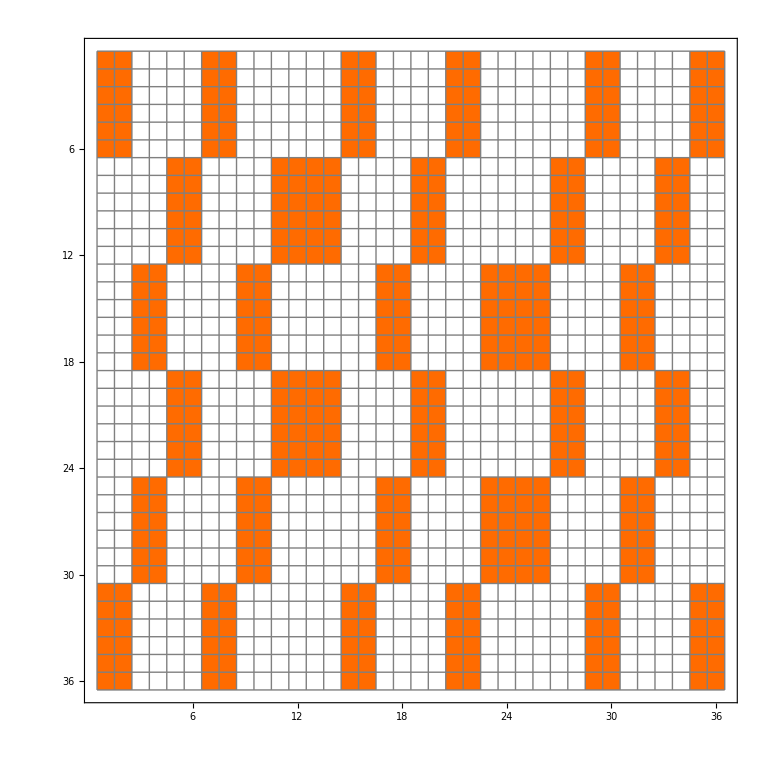

```mathematica
MM0={{1,0,0,0,0,0},{0,0,0,0,0,1},{0,1,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,1,0}};
overlayArray1=Unitize@Chop[numericalAMEfromOCTAVE, 10^-5];
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[overlayArray1]
```

## analytic AME constants

```mathematica
w=Exp[(ⅈ π)/10];
c=1/(√2);
a=c/(w+Conjugate[w]);
b=c/(w^3+Conjugate[w]^3);

aAltForm=1/(√(5+√5));
bAltForm=1/2 √(1/5 (5+√5));

{a^2+b^2+c^2,a^2+b^2-c^2,b/a}//FullSimplify 
N/@Re/@{a,b,aAltForm,bAltForm}
```

{1,0,1/2 (1+√5)}

{0.371748,0.601501,0.371748,0.601501}

## some initial form of AME (not used anymore)

1.+0. ⅈ

1.+0. ⅈ

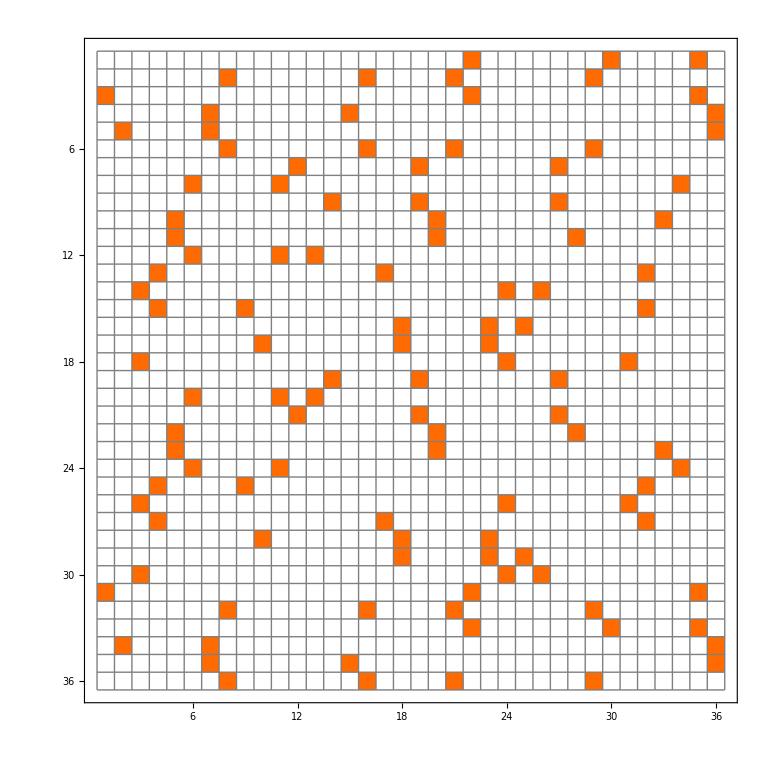

```mathematica
PC3=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}}); 
AME46AnotherForm=N[({{0, c, 0, 0, 0, 0, c, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, c w^17, 0, 0, 0, 0, 0, 0, c w^19, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^18, b w^3, 0, 0, 0, 0, b w^3, a w^18}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^3, b, 0, 0, 0, 0, b, a w^7, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b, a w^5, 0, 0, 0, 0, a w^5, b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^14, a w, 0, 0, 0, 0, a w^15, b w^12, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, c w^10, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^7, 0, 0, 0, 0, 0, 0, c w^19, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^2, b w^19, 0, 0, 0, 0, b w^13, a, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^10, 0, 0, 0, 0, 0, 0, c w^6, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, a w^2, b w, 0, 0, 0, 0, b w^5, a w^14, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b w^4, a w^3, 0, 0, 0, 0, a w^9, b w^18, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^8, 0, 0, 0, 0, 0, 0, c w^16, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^2, 0, 0, 0, 0, c w^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, c w^5, 0, 0, 0, 0, c w^19, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, a w, b w^10, 0, 0, 0, 0, b w^4, a w^3, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^13, 0, 0, 0, 0, 0, 0, c w^7, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^12, b w^15, 0, 0, 0, 0, b w, a w^14, 0, 0}, {0, 0, 0, 0, a w, b w^14, 0, 0, 0, 0, b w^16, a w^19, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {b w^10, a w^5, 0, 0, 0, 0, a w^15, b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^14, a w^7, 0, 0, 0, 0, a w^13, b w^16, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^10, a w^5, 0, 0, 0, 0, a w^5, b w^10}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a w^4, b w^17, 0, 0, 0, 0, b w^7, a w^10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a, b w^15, 0, 0, 0, 0, b w^15, a, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^14, 0, 0, 0, 0, c w^10, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, c w^10, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^7, a w^10, 0, 0, 0, 0, a, b w^13, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, 0, 0, c w^10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b w^2, a w^5, 0, 0, 0, 0, a w^15, b w^8, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {c, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c, 0, 0, 0, 0, c w^10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w^16, 0, 0, 0, 0, c, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {a w^10, b w^15, 0, 0, 0, 0, b w^5, a, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, b w^14, a w^3, 0, 0, 0, 0, a w^7, b w^6, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, c w, 0, 0, 0, 0, 0, 0, c w^11}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b w^9, a w^16, 0, 0, 0, 0, a w^16, b w^13, 0, 0, 0, 0}})];
ep@N[AME46AnotherForm]
gt@N[AME46AnotherForm]
MatrixPlot[Unitize@AME46AnotherForm,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}}];
P6={{1,0,0,0,0,0},{0,0,0,0,0,1},{0,1,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,1,0}};
overlayArray2=Unitize[Transpose@KroneckerProduct[P6,IdentityMatrix[6]].KroneckerProduct[IdentityMatrix[6],P6].Transpose@AME46AnotherForm].PC3;
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[overlayArray2]
```

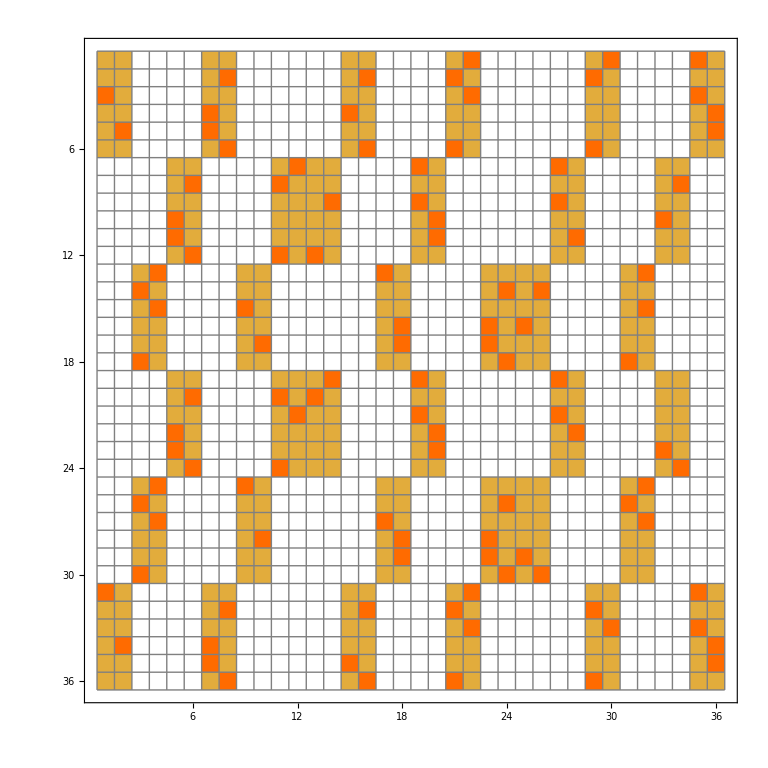

```mathematica
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[overlayArray1+overlayArray2]
```

## accepted form of AME

```mathematica
AME46=({{0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/5)/(√2), 0}, {0, ⅇ^((3 ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^((9 ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√(5+√5)), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(-(7 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, b ⅇ^((7 ⅈ π)/10), 0, 0, 0, 0, 0, 0, -b ⅈ}, {0, 0, 0, 0, 0, 0, b ⅇ^((ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, ⅇ^((ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√(5+√5))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅈ/(√(5+√5)), 0, 0, 0, 0, 0, 0, ⅇ^(-(ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, b ⅇ^((3 ⅈ π)/5), 0, 0, 0, 0, 0, 0}, {ⅇ^(-(ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, b ⅇ^((3 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/(√2), 0, 0, 0, 0, 0, 0, ⅇ^((4 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(3 ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, -1/(√2), 0, 0, 0, 0, 0, 0, 0, b ⅇ^((7 ⅈ π)/10), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, b ⅇ^(-(4 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^((ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(2 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, ⅇ^(-(4 ⅈ π)/5)/(√(5+√5))}, {0, 0, 0, 0, 0, 0, ⅇ^(-(9 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(2 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, b ⅇ^((ⅈ π)/10), 0, 0, 0, 0, 0, 0, b ⅇ^((ⅈ π)/10)}, {0, ⅇ^(-(2 ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(4 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(2 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, -ⅈ/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(7 ⅈ π)/10)/(√2), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((2 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((4 ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, b ⅇ^(-(3 ⅈ π)/5), 0, 0}, {0, 0, 0, 0, 0, b ⅇ^(-(3 ⅈ π)/10), 0, 0, 0, 0, ⅇ^((3 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√2), 0, 0, 0}, {0, 0, 0, 0, b ⅇ^(-(2 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(-(ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, -ⅈ/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^((9 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, b ⅇ^((4 ⅈ π)/5), 0, ⅇ^((ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√(5+√5)), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^((ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((ⅈ π)/5)/(√(5+√5)), 0, 0}, {0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, b ⅇ^(-(2 ⅈ π)/5), 0, ⅇ^(-(ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(-(4 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(4 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, -ⅈ/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, b ⅇ^(-(ⅈ π)/10), 0, 0, 0, 0, ⅇ^((4 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/5)/(√2), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((4 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, b ⅇ^(-(ⅈ π)/5), 0, 0}, {0, 0, 1/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(2 ⅈ π)/5), 0, 0, 0, 0, 0, 0, ⅇ^(-(7 ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^((ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(ⅈ π)/5)/(√(5+√5)), 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^((ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, b ⅇ^((3 ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, 0, -ⅈ/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, b ⅇ^((ⅈ π)/5), 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(ⅈ π)/5)/(√2), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^((4 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√2), 0, 0, 0, 0, 0}, {0, 0, b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, b ⅇ^(-(9 ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, ⅇ^((ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^((ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/10)/(√2), 0, 0, 0, 0, 0}, {0, 0, 0, b, 0, 0, 0, 0, ⅇ^(-(4 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/5)/(√2), 0, 0, 0, 0}, {0, 0, 0, ⅇ^(-(9 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, b ⅇ^(-(7 ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, 0, -ⅈ/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^((2 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((ⅈ π)/10)/(√(5+√5)), 0, 0, ⅇ^((7 ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^((ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b ⅇ^(-(3 ⅈ π)/10), 0, 0, 0, 0, 0, 0, ⅇ^((2 ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

## permutation matrices that bring (accepted) AME to block diagonal 9×(4×4) form

1.+0. ⅈ

1.+0. ⅈ

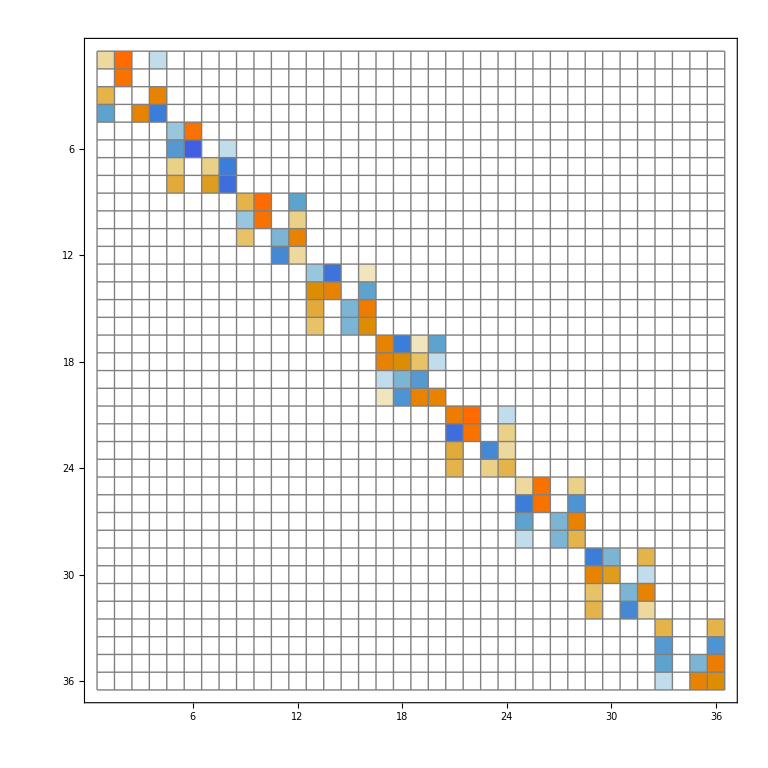

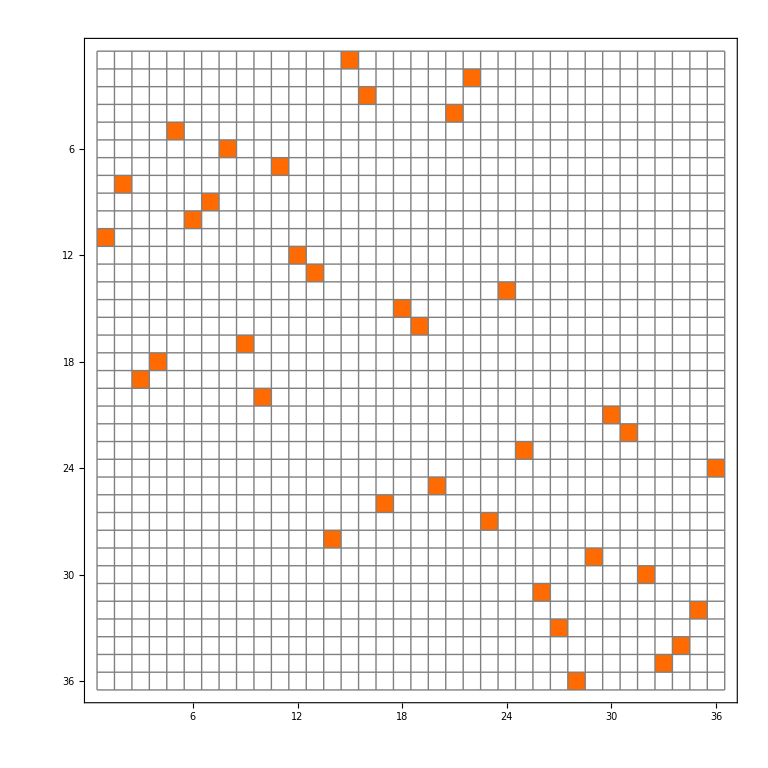

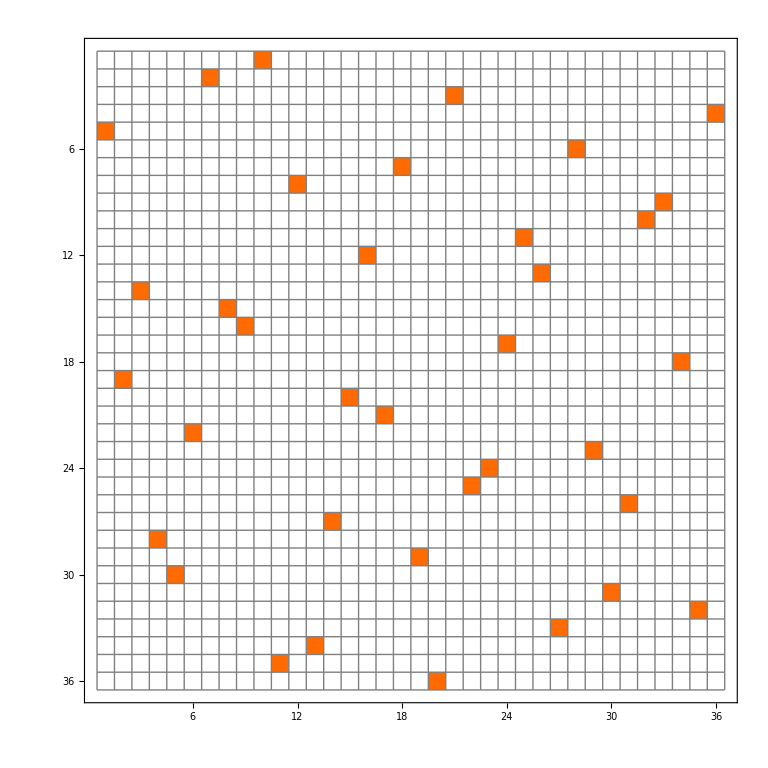

```mathematica
PR=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}}); 
PC=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}); 
(* PR^24 = PC^36 = Id *)
ep@N[AME46]
gt@N[AME46]
Y=PR.AME46.PC;
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[Y]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[PR]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[PC]
```

## "printable" form of (accepted) AME in form of block diagonal 3×(12×12) permuted by P

```mathematica
P36={
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
};
```

1.+0. ⅈ

1.+0. ⅈ

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

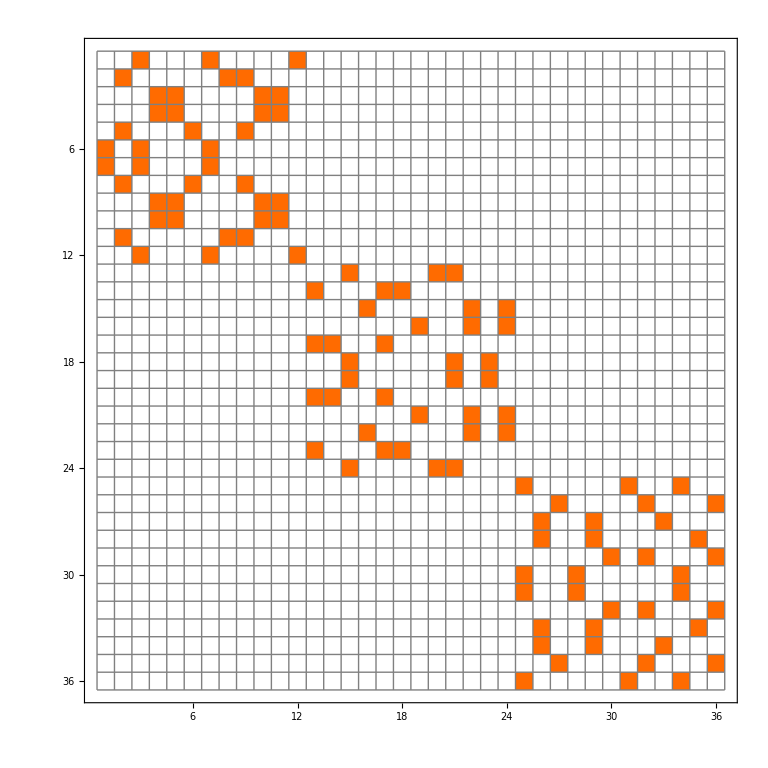

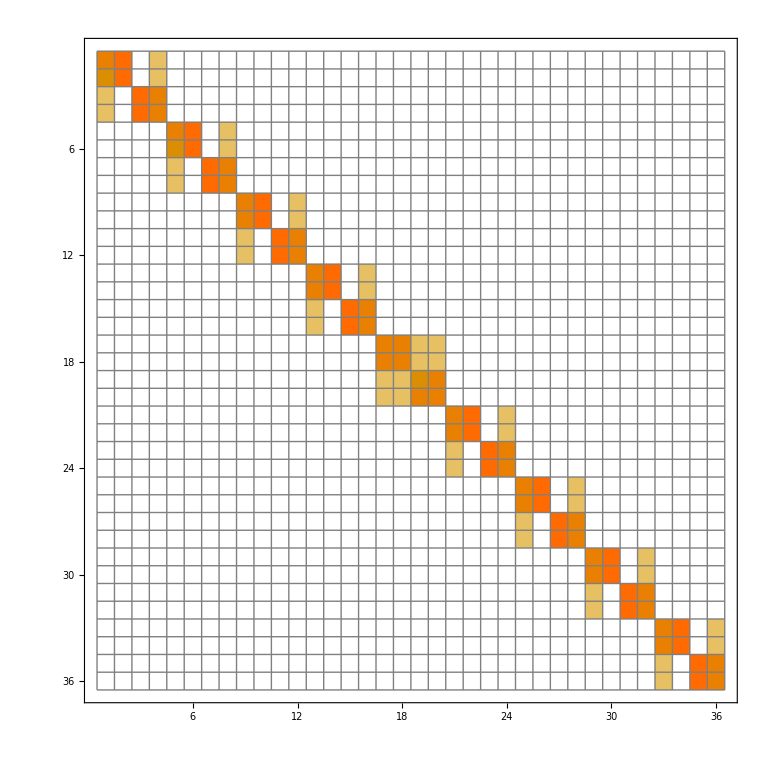

-Graphics-

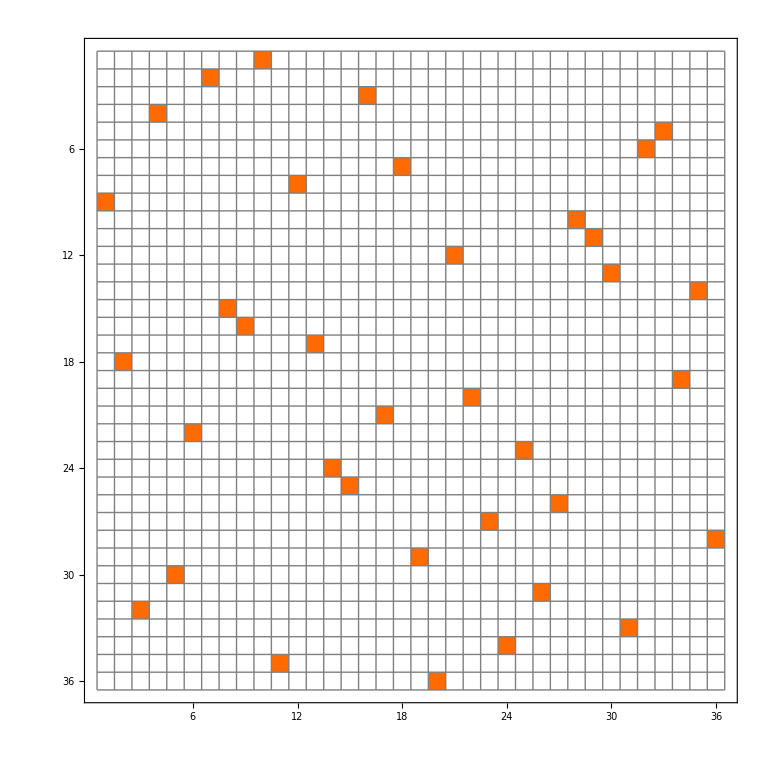

```mathematica
PR2=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}}); 
PC2=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}); 
(*B1={{0,0,b*w^19,0,0,0,a*w^18,0,0,0,0,c*w^6},{0,b*w^9,0,0,0,0,0,c*w^3,a,0,0,0},{0,0,0,b*w^7,b*w^15,0,0,0,0,a*w^13,a*w^14,0},{0,0,0,a*w^2,a*w^14,0,0,0,0,b*w^2,b*w^19,0},{0,a*w^5,0,0,0,c*w^19,0,0,b*w^6,0,0,0},{c*w^19,0,a*w^17,0,0,0,b*w^6,0,0,0,0,0},{c,0,a*w^8,0,0,0,b*w^17,0,0,0,0,0},{0,a*w^6,0,0,0,c*w^10,0,0,b*w^7,0,0,0},{0,0,0,a*w^16,a*w^12,0,0,0,0,b*w^12,b*w,0},{0,0,0,b*w,b*w,0,0,0,0,a*w^11,a*w^16,0},{0,b*w^12,0,0,0,0,0,c*w^16,a*w^3,0,0,0},{0,0,b*w^16,0,0,0,a*w^15,0,0,0,0,c*w^13}};
B2={{0,0,a,0,0,0,0,c*w^13,b*w^16,0,0,0},{a*w^18,0,0,0,b*w,c*w^14,0,0,0,0,0,0},{0,0,0,c*w^15,0,0,0,0,0,a*w,0,b*w^3},{0,0,0,0,0,0,c*w^18,0,0,b*w^2,0,a*w^14},{b*w^8,c*w^14,0,0,a*w,0,0,0,0,0,0,0},{0,0,b,0,0,0,0,0,a*w^6,0,c,0},{0,0,b*w^11,0,0,0,0,0,a*w^17,0,c*w,0},{b*w,c*w^17,0,0,a*w^14,0,0,0,0,0,0,0},{0,0,0,0,0,0,c*w^6,0,0,b,0,a*w^12},{0,0,0,c*w^15,0,0,0,0,0,a*w^11,0,b*w^13},{a*w,0,0,0,b*w^4,c*w^7,0,0,0,0,0,0},{0,0,a*w,0,0,0,0,c*w^4,b*w^17,0,0,0}};
B3={{a*w^4,0,0,0,0,0,c*w^8,0,0,b*w^14,0,0},{0,0,c*w^14,0,0,0,0,a*w^6,0,0,0,b*w^17},{0,a*w^6,0,0,b*w^16,0,0,0,c,0,0,0},{0,b*w^19,0,0,a*w^19,0,0,0,0,0,c*w^15,0},{0,0,0,0,0,c*w,0,b*w^8,0,0,0,a*w^9},{b,0,0,c*w^14,0,0,0,0,0,a,0,0},{b*w^2,0,0,c*w^6,0,0,0,0,0,a*w^2,0,0},{0,0,0,0,0,c*w^19,0,b*w^16,0,0,0,a*w^17},{0,b*w^12,0,0,a*w^12,0,0,0,0,0,c*w^18,0},{0,a*w^15,0,0,b*w^5,0,0,0,c*w^19,0,0,0},{0,0,c*w^6,0,0,0,0,a*w^8,0,0,0,b*w^19},{a*w^8,0,0,0,0,0,c*w^2,0,0,b*w^18,0,0}};*)

(* WATCH OUT - REDEFINITION OF a, b and c CONSTANTS!!! *)
w=Exp[I π 2/20];
a=1/(√2);
b=a/(w+Conjugate[w]);
c=a/(w^3+Conjugate[w^3]);
B1={{0,0,c w^19,0,0,0,b w^18,0,0,0,0,a w^6},{0,c w^9,0,0,0,0,0,a w^3,b,0,0,0},{0,0,0,c w^7,c w^15,0,0,0,0,b w^13,b w^14,0},{0,0,0,b w^2,b w^14,0,0,0,0,c w^2,c w^19,0},{0,b w^5,0,0,0,a w^19,0,0,c w^6,0,0,0},{a w^19,0,b w^17,0,0,0,c w^6,0,0,0,0,0},{a,0,b w^8,0,0,0,c w^17,0,0,0,0,0},{0,b w^6,0,0,0,a w^10,0,0,c w^7,0,0,0},{0,0,0,b w^16,b w^12,0,0,0,0,c w^12,c w,0},{0,0,0,c w,c w,0,0,0,0,b w^11,b w^16,0},{0,c w^12,0,0,0,0,0,a w^16,b w^3,0,0,0},{0,0,c w^16,0,0,0,b w^15,0,0,0,0,a w^13}};

B2={{0,0,b,0,0,0,0,a w^13,c w^16,0,0,0},{b w^18,0,0,0,c w,a w^14,0,0,0,0,0,0},{0,0,0,a w^15,0,0,0,0,0,b w,0,c w^3},{0,0,0,0,0,0,a w^18,0,0,c w^2,0,b w^14},{c w^8,a w^14,0,0,b w,0,0,0,0,0,0,0},{0,0,c,0,0,0,0,0,b w^6,0,a,0},{0,0,c w^11,0,0,0,0,0,b w^17,0,a w,0},{c w,a w^17,0,0,b w^14,0,0,0,0,0,0,0},{0,0,0,0,0,0,a w^6,0,0,c,0,b w^12},{0,0,0,a w^15,0,0,0,0,0,b w^11,0,c w^13},{b w,0,0,0,c w^4,a w^7,0,0,0,0,0,0},{0,0,b w,0,0,0,0,a w^4,c w^17,0,0,0}};

B3={{b w^4,0,0,0,0,0,a w^8,0,0,c w^14,0,0},{0,0,a w^14,0,0,0,0,b w^6,0,0,0,c w^17},{0,b w^6,0,0,c w^16,0,0,0,a,0,0,0},{0,c w^19,0,0,b w^19,0,0,0,0,0,a w^15,0},{0,0,0,0,0,a w,0,c w^8,0,0,0,b w^9},{c,0,0,a w^14,0,0,0,0,0,b,0,0},{c w^2,0,0,a w^6,0,0,0,0,0,b w^2,0,0},{0,0,0,0,0,a w^19,0,c w^16,0,0,0,b w^17},{0,c w^12,0,0,b w^12,0,0,0,0,0,a w^18,0},{0,b w^15,0,0,c w^5,0,0,0,a w^19,0,0,0},{0,0,a w^6,0,0,0,0,b w^8,0,0,0,c w^19},{b w^8,0,0,0,0,0,a w^2,0,0,c w^18,0,0}};
PrintableAME0=ArrayFlatten[{
{B1,0,0},
{0,B2,0},
{0,0,B3}
}];
PrintableAME=PrintableAME0.Transpose[P36]//N;
ep@N[PrintableAME]
gt@N[PrintableAME]
SL/@{PrintableAME,RF@PrintableAME,T2@PrintableAME}
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[Unitize@PrintableAME0]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[Abs[PR2.PrintableAME.PC2]]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[PR2]
MatrixPlot[#,Mesh->All,PlotTheme->"Default",FrameStyle->Opacity[1],MeshStyle->Directive[Gray],FrameTicksStyle->Directive[Black,22],FrameTicks->{{6,12,18,24,30,36},{6,12,18,24,30,36}},ImageSize->768]&[PC2]
```

```mathematica
UnitaryMatrixQ/@{B1,B2,B3}
```

{True,True,True}

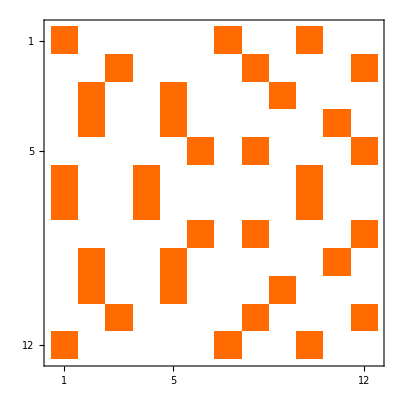

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Unitize@B3//MatrixPlot
Abs[Eigenvalues[B3]]//N
```